```mathematica
ab = {{0.5, 0.5}, {5, 1}, {1, 3}, {2, 2}, {2, 5}}
?Функция плотности распределения
f[t_, a_, b_] =  (Gamma[a+b] * t ^ (a-1) * (1-t)^(b-1)) /(Gamma[a]*Gamma[b]) 
?Функция распределения
F[t_, a_, b_] = Integrate[f[x, a, b], {x, 0, t}]
?Начальные моменты
a1[a_, b_] =Integrate[x*f[x, a, b], {x, 0, 1}]
a2[a_, b_] =Integrate[x^2*f[x, a, b], {x, 0, 1}]
a3[a_, b_] =Integrate[x^3*f[x, a, b], {x, 0, 1}]
?Математическое ожидание
mean[a_, b_] = a / (a + b)
?Дисперсия
variance[a_, b_] = (a * b) / ((a + b)^2 * (a + b + 1) ) 
?Среднее квадратическое отклонение
deviance1[a_, b_] = Sqrt[variance1[a, b]]
deviance2[a_, b_] = Sqrt[variance2[a,b]]
?Маасив случайных чисел
arrSize = 10000
randArr =RandomReal[{0,1}, arrSize]




Print[randFuncValArr[[arrSize]]]
```

{{0.5,0.5},{5,1},{1,3},{2,2},{2,5}}

Information[Функция плотности распределения,LongForm→False]

((1-t)^(-1+b) t^(-1+a) Gamma[a+b])/(Gamma[a] Gamma[b])

Information[Функция распределения,LongForm→False]

ConditionalExpression[(Beta[t,a,b] Gamma[a+b])/(Gamma[a] Gamma[b]),Re[a]>0&&(Re[t]≤1||t∉ℝ)]

Information[моменты Начальные,LongForm→False]

ConditionalExpression[(Gamma[1+a] Gamma[a+b])/(Gamma[a] Gamma[1+a+b]),Re[a]>-1&&Re[b]>0]

ConditionalExpression[(Gamma[2+a] Gamma[a+b])/(Gamma[a] Gamma[2+a+b]),Re[a]>-2&&Re[b]>0]

ConditionalExpression[(Gamma[3+a] Gamma[a+b])/(Gamma[a] Gamma[3+a+b]),Re[a]>-3&&Re[b]>0]

Missing[UnknownSymbol,Математическое ожидание]

a/(a+b)

Missing[UnknownSymbol,Дисперсия]

(a b)/((a+b)^2 (1+a+b))

Information[Среднее отклонение квадратическое,LongForm→False]

√variance1[a,b]

√variance2[a,b]

Information[чисел Маасив случайных,LongForm→False]

10000

{0.870483,0.24609,0.504842,0.281972,0.038404,0.1428,0.515443,0.884972,0.547436,0.92664,0.164191,0.637414,0.147947,0.147722,0.293508,0.737356,0.41045,0.582611,0.0407759,0.915887,0.496731,0.720177,0.660118,0.385312,0.628782,0.433237,0.0812898,0.772332,0.884746,0.000216021,0.851182,0.478238,0.328843,0.924069,0.158464,0.310973,0.357654,0.697517,0.00237093,0.959276,0.294706,0.132396,0.212485,0.0455553,0.792416,0.872352,0.0142331,0.918019,0.818228,0.886976,0.875378,0.869692,0.577198,0.543028,0.953586,0.310709,0.516308,0.909709,0.0965985,0.239802,0.0185208,0.314636,0.624055,0.66422,0.281776,0.449566,0.339746,0.768695,0.513231,0.976069,0.191926,0.955177,0.0152427,0.0801751,0.810059,0.695131,0.483047,0.354444,0.662824,0.592318,0.387652,0.657699,0.112656,0.279967,0.384457,0.622947,0.102474,0.613893,0.0361592,0.525822,0.604199,0.274109,0.672107,0.319806,0.485298,0.52113,0.028217,0.308362,0.446165,0.758523,0.483552,0.0419875,0.0800428,0.853309,0.0764531,0.633068,0.0111334,0.734032,0.717004,0.79725,0.834096,0.235447,0.184481,0.688477,0.62631,0.786185,0.702672,0.559511,0.0271028,0.345696,0.07845,0.233298,0.46338,0.712825,0.372653,0.754258,0.812554,0.885702,0.439879,0.242924,0.0112028,0.773991,0.463055,0.733105,0.138693,0.617157,0.36906,0.302749,0.754043,0.587432,0.648338,0.640754,0.711357,0.227229,0.510335,0.237575,0.509456,0.249709,0.69172,0.177634,0.291396,0.55865,0.213908,0.940624,0.893361,0.32805,0.0367153,0.710905,0.0381884,0.934926,0.689861,0.0582375,0.93761,0.0287496,0.834626,0.181146,0.329679,0.150371,0.353022,0.302774,0.67659,0.410602,0.64628,0.782807,0.129219,0.853988,0.77971,0.830936,0.981629,0.520425,0.206608,0.0857571,0.236973,0.752397,0.0180976,0.167931,0.465438,0.395644,0.910865,0.331426,0.160714,0.205903,0.965217,0.967236,0.443381,0.884559,0.655286,0.909949,0.37661,0.969149,0.687792,0.672607,0.498485,0.299576,0.300443,0.190452,0.596753,0.142007,0.447099,0.064755,0.75306,0.890763,0.616004,0.0873212,0.889686,0.128887,0.160179,0.651417,0.63445,0.542095,0.261644,0.302564,0.596074,0.36551,0.444399,0.582038,0.947802,0.823516,0.708349,0.442983,0.68459,0.17223,0.0872024,0.700993,0.561073,0.634182,0.973728,0.875041,0.755912,0.158847,0.358711,0.556295,0.530586,0.709555,0.460723,0.449762,0.208449,0.406914,0.482239,0.479848,0.488532,0.0249703,0.153148,0.796847,0.282457,0.245594,0.469189,0.699157,0.0089897,0.555405,0.349301,0.433407,0.691205,0.601525,0.673419,0.0887979,0.805425,0.752974,0.759538,0.716061,0.766359,0.351439,0.431104,0.541552,0.0703389,0.532438,0.475356,0.802843,0.999417,0.912987,0.913616,0.0725251,0.520442,0.343452,0.186227,0.897572,0.0277912,0.923456,0.0247328,0.366981,0.539265,0.843264,0.27461,0.988948,0.79822,0.693864,0.768078,0.839756,0.245905,0.805038,0.225349,0.539168,0.593925,0.576137,0.68751,0.388802,0.478373,0.534517,0.858662,0.26082,0.880054,0.196071,0.405779,0.321995,0.350177,0.488464,0.882282,0.908489,0.672251,0.414933,0.240503,0.391697,0.100659,0.0864772,0.779663,0.468045,0.217879,0.0216317,0.160335,0.12306,0.135062,0.316462,0.883629,0.643404,0.217308,0.86519,0.112891,0.70941,0.757792,0.449048,0.0922144,0.673991,0.981742,0.606499,0.532611,0.34978,0.978679,0.765331,0.848323,0.00487647,0.29376,0.778307,0.655966,0.443504,0.732457,0.256373,0.472034,0.229168,0.731485,0.702617,0.325155,0.708338,0.245471,0.192609,0.423026,0.643503,0.810198,0.695071,0.791381,0.0936588,0.165357,0.215396,0.205766,0.76799,0.993153,0.256219,0.30583,0.773056,0.259054,0.784296,0.48531,0.592452,0.282437,0.16749,0.670039,0.768635,0.98356,0.324581,0.578721,0.0315117,0.955493,0.911804,0.0463901,0.130702,0.515125,0.983976,0.602221,0.895439,0.888361,0.277637,0.631322,0.949256,0.664974,0.0545917,0.653272,0.883733,0.268634,0.0996539,0.396309,0.806379,0.456099,0.000908945,0.687045,0.00176889,0.153242,0.554492,0.736078,0.830215,0.688533,0.288351,0.972824,0.312773,0.00977778,0.413329,0.264047,0.338586,0.2214,0.515045,0.846114,0.704914,0.87612,0.386884,0.271562,0.964829,0.515322,0.11899,0.849839,0.65893,0.656092,0.461401,0.0178317,0.737304,0.0611234,0.448955,0.849918,0.527029,0.705688,0.11286,0.726264,0.671362,0.59284,0.0611023,0.970612,0.1611,0.971912,0.896085,0.511751,0.103257,0.0056798,0.947705,0.971037,0.0989546,0.472636,0.0982956,0.455543,0.330744,0.110724,0.720812,0.832351,0.928619,0.202245,0.635957,0.85659,0.777278,0.257339,0.621653,0.78091,0.81408,0.515129,0.739117,0.71391,0.581549,0.214367,0.826709,0.558535,0.550572,0.696445,0.164004,0.261565,0.778175,0.21262,0.480739,0.414322,0.138077,0.63365,0.242516,0.661483,0.665606,0.976888,0.0710313,0.336432,0.254586,0.14082,0.552415,0.875594,0.531726,0.0806516,0.473379,0.970973,0.566594,0.173027,0.195679,0.188031,0.279491,0.594614,0.29847,0.997767,0.926849,0.602487,0.552548,0.429886,0.465466,0.198947,0.347511,0.743071,0.212681,0.0741446,0.887271,0.390259,0.629469,0.391714,0.294564,0.472081,0.0185035,0.28688,0.565665,0.937168,0.89262,0.688976,0.184181,0.956746,0.828604,0.115008,0.820025,0.52817,0.21463,0.743652,0.590842,0.75705,0.667761,0.881984,0.609722,0.406933,0.797781,0.596606,0.347029,0.915576,0.300561,0.063502,0.145548,0.290622,0.933279,0.06102,0.277839,0.833221,0.270609,0.243728,0.0597302,0.568074,0.685585,0.126504,0.874527,0.197189,0.97059,0.64794,0.0966154,0.273607,0.388194,0.495058,0.139475,0.566817,0.16227,0.237213,0.0380007,0.0566107,0.557479,0.644953,0.159632,0.338065,0.483204,0.97795,0.924211,0.401154,0.789464,0.913249,0.254541,0.370016,0.81213,0.348187,0.573916,0.0545441,0.730111,0.215693,0.699833,0.703053,0.492549,0.476312,0.460762,0.803595,0.965601,0.394396,0.214287,0.165654,0.97787,0.361145,0.114568,0.0397905,0.535056,0.85519,0.425988,0.510296,0.0225148,0.22507,0.961608,0.254328,0.429694,0.954443,0.144997,0.812496,0.732281,0.185461,0.351486,0.191603,0.486304,0.7183,0.778412,0.0499462,0.410962,0.944468,0.0410975,0.0789647,0.224991,0.336579,0.182385,0.817452,0.830876,0.39791,0.76029,0.130437,0.772967,0.809778,0.172725,0.469385,0.518874,0.655796,0.0671822,0.44455,0.210947,0.126359,0.312874,0.0146645,0.170689,0.366321,0.653346,0.81816,0.379958,0.555162,0.641087,0.572307,0.267992,0.612892,0.814406,0.665565,0.288851,0.199479,0.538118,0.497174,0.809744,0.546261,0.532773,0.148208,0.318267,0.684104,0.51534,0.173893,0.928292,0.975634,0.566652,0.104973,0.215037,0.233941,0.305627,0.443943,0.51503,0.340685,0.497597,0.00689832,0.93271,0.86652,0.205872,0.410482,0.0829459,0.727381,0.334752,0.455106,0.288648,0.981032,0.101434,0.748527,0.862048,0.411171,0.343786,0.945445,0.110133,0.488236,0.502574,0.12833,0.304129,0.585707,0.0751308,0.350015,0.685119,0.704083,0.63243,0.380169,0.231209,0.756197,0.443724,0.351781,0.715001,0.859642,0.0731254,0.989404,0.390576,0.438726,0.763365,0.703191,0.188575,0.431059,0.186565,0.206461,0.905956,0.637623,0.117104,0.315033,0.527996,0.584993,0.408045,0.363284,0.681986,0.142239,0.951008,0.337307,0.305178,0.0244217,0.817955,0.495156,0.891603,0.681848,0.762465,0.0731728,0.293829,0.401872,0.594249,0.627887,0.242,0.851899,0.00272899,0.371415,0.642094,0.110442,0.10888,0.339917,0.981821,0.226574,0.143024,0.584549,0.992133,0.60146,0.310628,0.863987,0.289456,0.458375,0.603176,0.105514,0.440834,0.418354,0.473415,0.493262,0.905321,0.267857,0.754497,0.28313,0.827882,0.707806,0.739176,0.595797,0.0807169,0.919967,0.233541,0.338779,0.937667,0.959035,0.668964,0.165928,0.676406,0.497715,0.753338,0.736139,0.879791,0.056113,0.533046,0.0498933,0.35106,0.295146,0.466021,0.517147,0.546818,0.818237,0.76439,0.177464,0.519738,0.360165,0.947893,0.350918,0.98899,0.649713,0.523661,0.600072,0.48015,0.522589,0.697766,0.0627893,0.415735,0.243147,0.475756,0.291414,0.883083,0.672464,0.174637,0.508422,0.427408,0.682938,0.111452,0.76708,0.768515,0.230817,0.176273,0.137954,0.423745,0.966808,0.996435,0.857067,0.290457,0.291307,0.691746,0.0631116,0.121981,0.47313,0.716036,0.188477,0.610314,0.407323,0.825179,0.769964,0.179357,0.827611,0.627428,0.266603,0.7185,0.108234,0.771837,0.700516,0.602014,0.872252,0.121511,0.411527,0.502915,0.630668,0.970461,0.315612,0.622431,0.216162,0.416334,0.158406,0.308472,0.247016,0.307855,0.627518,0.0211388,0.520555,0.621542,0.923527,0.995826,0.900435,0.873,0.637499,0.719534,0.996161,0.62069,0.146406,0.0642968,0.170419,0.493283,0.603709,0.122811,0.813896,0.675644,0.59935,0.626702,0.798284,0.570513,0.911691,0.338988,0.745575,0.430314,0.27596,0.0534877,0.909529,0.11599,0.55144,0.59534,0.571779,0.42254,0.69153,0.950163,0.864375,0.881269,0.781136,0.406852,0.738853,0.859641,0.934296,0.576863,0.461127,0.614,0.713805,0.533449,0.0793902,0.847897,0.204266,0.139264,0.509649,0.0802836,0.45485,0.253071,0.543286,0.999134,0.485935,0.129263,0.809971,0.290366,0.697673,0.825944,0.348531,0.284955,0.200644,0.156669,0.0854793,0.504099,0.040202,0.126484,0.530184,0.261475,0.556494,0.619555,0.843951,0.988687,0.831161,0.0419333,0.704391,0.0744547,0.830464,0.180275,0.301637,0.108636,0.7834,0.961873,0.0659498,0.242459,0.418055,0.156834,0.394236,0.245113,0.36305,0.774803,0.180712,0.986374,0.309618,0.876449,0.48031,0.735906,0.0665194,0.108498,0.0581689,0.464875,0.542423,0.15744,0.870006,0.641072,0.952017,0.102477,0.674426,0.228891,0.465082,0.100128,0.104606,0.238899,0.957641,0.0323132,0.0581981,0.62759,0.980539,0.775563,0.350849,0.534331,0.699525,0.325748,0.888058,0.38429,0.13501,0.233008,0.918187,0.0929723,0.643705,0.73867,0.562136,0.436827,0.718064,0.437965,0.980644,0.340996,0.156601,0.863166,0.104711,0.38364,0.924042,0.855301,0.984218,0.715502,0.875703,0.750397,0.17992,0.127187,0.824443,0.879462,0.533951,0.825846,0.463774,0.0507255,0.603188,0.475561,0.447207,0.49957,0.392918,0.134559,0.121416,0.0418637,0.691543,0.14272,0.281307,0.623996,0.0289001,0.536117,0.660548,0.0134675,0.670359,0.144782,0.482406,0.840357,0.569474,0.190662,0.493482,0.965128,0.872277,0.378322,0.456362,0.858046,0.163228,0.577907,0.923617,0.74835,0.057527,0.959775,0.778909,0.340425,0.108312,0.967226,0.488345,0.601568,0.95251,0.143667,0.0577574,0.522229,0.242175,0.44891,0.462125,0.954046,0.50189,0.290602,0.334142,0.00413377,0.0992228,0.573136,0.0676526,0.382626,0.257288,0.287069,0.478821,0.47365,0.747032,0.00166629,0.165977,0.43241,0.789996,0.425345,0.701306,0.791632,0.428045,0.479669,0.708149,0.476377,0.50425,0.251263,0.702148,0.230306,0.735759,0.903169,0.256827,0.436417,0.260482,0.0577958,0.0906872,0.901122,0.967214,0.997649,0.875073,0.577914,0.202474,0.164112,0.42942,0.39443,0.638404,0.862607,0.482276,0.918617,0.859151,0.511724,0.506452,0.553205,0.144048,0.876404,0.412653,0.0141465,0.203694,0.988379,0.922784,0.663125,0.667204,0.974026,0.424744,0.733682,0.117345,0.839366,0.539794,0.703372,0.88011,0.0610107,0.774947,0.792771,0.912248,0.748372,0.055603,0.18322,0.0457514,0.48711,0.97017,0.728493,0.393285,0.137901,0.00983327,0.214487,0.76848,0.792805,0.779974,0.401789,0.400919,0.417572,0.376826,0.552389,0.961296,0.309545,0.876248,0.0199046,0.113685,0.0364224,0.879166,0.429865,0.368983,0.10256,0.0421927,0.751215,0.819449,0.628373,0.573854,0.484452,0.132589,0.84092,0.190498,0.240428,0.673773,0.361258,0.653119,0.50073,0.280465,0.479334,0.240831,0.49459,0.296587,0.403354,0.373644,0.239957,0.292964,0.091591,0.711619,0.423427,0.467072,0.311991,0.160714,0.212461,0.567447,0.566339,0.479965,0.325648,0.502109,0.775387,0.407178,0.14602,0.362026,0.390942,0.360608,0.0231797,0.00315139,0.0844189,0.382409,0.484396,0.4578,0.778112,0.77307,0.292027,0.0867966,0.939369,0.822474,0.81516,0.621493,0.15149,0.305529,0.666034,0.657122,0.653508,0.833027,0.573773,0.399185,0.0938491,0.0581697,0.126033,0.347261,0.415439,0.690386,0.202277,0.868426,0.780243,0.0605491,0.548177,0.827054,0.657721,0.885437,0.851181,0.379596,0.229306,0.754548,0.972343,0.734564,0.297733,0.401647,0.664436,0.993111,0.853024,0.690505,0.0607601,0.243915,0.388819,0.493731,0.342001,0.51672,0.01361,0.806575,0.742202,0.907602,0.930649,0.0137752,0.528297,0.175225,0.163408,0.440584,0.76932,0.330248,0.477563,0.0877137,0.725729,0.098541,0.723774,0.00822937,0.324262,0.405041,0.168613,0.20026,0.053707,0.974709,0.504751,0.249564,0.24852,0.530009,0.769292,0.139654,0.653762,0.672492,0.637745,0.648306,0.680725,0.493726,0.350916,0.668791,0.0885007,0.348296,0.49577,0.332877,0.622347,0.539954,0.371852,0.457937,0.497329,0.762619,0.369667,0.513341,0.64406,0.981496,0.201502,0.196627,0.489882,0.973031,0.519674,0.450792,0.625816,0.879366,0.437097,0.407814,0.56347,0.845534,0.281617,0.291803,0.394896,0.591347,0.593814,0.40607,0.147026,0.161762,0.326823,0.302478,0.975785,0.198913,0.094276,0.926628,0.68277,0.370752,0.194242,0.464636,0.769247,0.00188421,0.0699281,0.441988,0.325092,0.775897,0.442759,0.694147,0.909688,0.791312,0.475619,0.177073,0.437822,0.643518,0.773942,0.715991,0.320789,0.0823327,0.18973,0.411382,0.218732,0.277813,0.0121231,0.615679,0.479933,0.268712,0.36974,0.159664,0.454985,0.869688,0.157593,0.708352,0.11266,0.852095,0.946142,0.753819,0.624404,0.177909,0.252552,0.218686,0.474894,0.403892,0.962351,0.915761,0.729405,0.574172,0.131698,0.895264,0.0429878,0.384491,0.468718,0.643126,0.575492,0.275194,0.598908,0.192653,0.604141,0.000642316,0.661857,0.0431415,0.177422,0.978417,0.919996,0.669805,0.55744,0.44134,0.632002,0.342698,0.345748,0.625331,0.589336,0.561984,0.443276,0.841474,0.692689,0.16852,0.0931908,0.545373,0.119124,0.188262,0.533025,0.721158,0.843257,0.592537,0.931886,0.26043,0.966575,0.290804,0.501771,0.559865,0.440426,0.602435,0.767605,0.673327,0.373602,0.135136,0.886665,0.535069,0.687458,0.890702,0.340519,0.549775,0.979555,0.523643,0.26268,0.00812223,0.31235,0.383375,0.483599,0.481477,0.332568,0.359312,0.393084,0.871229,0.521505,0.697662,0.695313,0.702285,0.620527,0.663412,0.153375,0.772479,0.346073,0.584019,0.817404,0.947155,0.241668,0.926521,0.547415,0.699723,0.679616,0.334162,0.579576,0.408879,0.256278,0.240659,0.786629,0.379727,0.202069,0.0409072,0.312303,0.958529,0.351999,0.152523,0.379806,0.164132,0.966646,0.677544,0.852146,0.616577,0.0111365,0.387984,0.0811397,0.825522,0.396558,0.0943682,0.834915,0.0838618,0.207729,0.143226,0.270424,0.673223,0.84991,0.841907,0.0299798,0.535718,0.934908,0.975234,0.193471,0.133793,0.282899,0.932267,0.628779,0.927489,0.707388,0.708846,0.316412,0.757671,0.987851,0.168427,0.91095,0.602144,0.41884,0.239122,0.780504,0.507777,0.985925,0.35629,0.99432,0.569262,0.309745,0.680627,0.942872,0.383443,0.602808,0.87897,0.0240814,0.202236,0.0188746,0.275293,0.713769,0.738452,0.534045,0.305189,0.421416,0.269782,0.862328,0.329418,0.332671,0.938235,0.354889,0.146671,0.474703,0.407255,0.196384,0.635308,0.36489,0.404567,0.00958341,0.785042,0.319175,0.606245,0.278541,0.710687,0.988012,0.18354,0.857769,0.722476,0.889167,0.973821,0.207308,0.515192,0.991615,0.594309,0.19533,0.302338,0.266004,0.618811,0.989382,0.115109,0.0544896,0.848633,0.157215,0.104522,0.990393,0.436267,0.933293,0.0652841,0.13534,0.574308,0.843358,0.801372,0.715365,0.46592,0.166273,0.337987,0.605951,0.696402,0.0830718,0.313497,0.100118,0.658119,0.350295,0.396958,0.173949,0.908162,0.814168,0.515428,0.791753,0.906346,0.613913,0.337394,0.241659,0.283235,0.962591,0.421426,0.624281,0.893933,0.172133,0.016244,0.108618,0.0737512,0.0693365,0.769595,0.96828,0.392705,0.554592,0.482962,0.00656814,0.327008,0.192158,0.544811,0.0107593,0.983444,0.766107,0.395669,0.451515,0.246221,0.817553,0.784706,0.248092,0.951352,0.879773,0.425399,0.962809,0.284494,0.997484,0.849955,0.960669,0.275753,0.354963,0.185361,0.849271,0.19477,0.74036,0.99471,0.585743,0.922403,0.799401,0.859885,0.129635,0.92468,0.678508,0.56838,0.625234,0.247141,0.722188,0.20631,0.520588,0.628121,0.693963,0.851879,0.283186,0.499463,0.0865652,0.63897,0.670802,0.522165,0.862243,0.307726,0.60193,0.132512,0.255329,0.0574558,0.624557,0.547824,0.357978,0.0663253,0.404935,0.891283,0.606604,0.24301,0.416046,0.734888,0.731236,0.477437,0.129236,0.450882,0.100244,0.420067,0.127627,0.317711,0.983409,0.71604,0.955535,0.198985,0.674923,0.108096,0.490425,0.807858,0.858343,0.588454,0.177258,0.892467,0.0676665,0.620381,0.278681,0.480935,0.042245,0.281539,0.882141,0.576928,0.77351,0.672198,0.714245,0.00124303,0.689002,0.862538,0.437662,0.993936,0.299286,0.13964,0.809667,0.207307,0.259285,0.923421,0.285117,0.249918,0.164737,0.683583,0.125601,0.806705,0.57876,0.573794,0.772256,0.3297,0.284011,0.269321,0.414566,0.182823,0.423013,0.130534,0.369026,0.0225343,0.762735,0.155164,0.594224,0.246529,0.575389,0.0863111,0.0399604,0.479537,0.213479,0.332019,0.599553,0.312368,0.910681,0.268194,0.740671,0.658896,0.775775,0.107153,0.00572939,0.747972,0.915491,0.523423,0.0676126,0.0743373,0.196229,0.659658,0.537876,0.682607,0.100293,0.836954,0.612032,0.37816,0.0140704,0.275352,0.925603,0.0209235,0.733753,0.91332,0.589858,0.516855,0.752972,0.445902,0.675933,0.732702,0.00794333,0.832466,0.181905,0.594397,0.522702,0.959285,0.9833,0.692906,0.988581,0.932504,0.585775,0.31638,0.7829,0.501583,0.315402,0.594728,0.792824,0.26275,0.386291,0.604661,0.74599,0.0906473,0.189086,0.457482,0.668945,0.121379,0.0992927,0.832549,0.472126,0.212136,0.623997,0.697944,0.836639,0.730678,0.864786,0.0301327,0.969915,0.826419,0.795582,0.58868,0.863692,0.713739,0.185172,0.747148,0.601162,0.249358,0.564253,0.605283,0.497428,0.363081,0.721059,0.58721,0.0789203,0.299133,0.967116,0.053063,0.558954,0.829025,0.348933,0.815261,0.903877,0.830494,0.137707,0.448552,0.142901,0.536321,0.268029,0.867451,0.756835,0.237556,0.18112,0.684346,0.864181,0.773541,0.108018,0.061697,0.22963,0.126615,0.927151,0.723079,0.597308,0.146949,0.194024,0.648952,0.816986,0.121426,0.155463,0.969907,0.996293,0.242249,0.621421,0.784931,0.330596,0.574987,0.512784,0.0830712,0.921127,0.847814,0.961002,0.346858,0.884767,0.80951,0.127037,0.334926,0.217795,0.0492175,0.0744176,0.587019,0.100249,0.44705,0.11866,0.64673,0.0534944,0.15977,0.146496,0.399254,0.237202,0.398124,0.0908259,0.501182,0.0869899,0.710373,0.846389,0.858588,0.473413,0.783849,0.402734,0.0059401,0.00889071,0.070709,0.252051,0.701378,0.94934,0.932911,0.498974,0.749578,0.8057,0.819996,0.954974,0.639095,0.741132,0.516276,0.664628,0.600364,0.534926,0.299077,0.474906,0.88754,0.714918,0.83377,0.607463,0.961316,0.339696,0.682261,0.742436,0.105164,0.50695,0.0551588,0.0472147,0.238886,0.216029,0.36333,0.776122,0.640142,0.298859,0.508233,0.635291,0.687849,0.585269,0.987368,0.138927,0.099289,0.0944981,0.110832,0.0887392,0.691546,0.57831,0.0951228,0.920505,0.311125,0.315738,0.08601,0.869103,0.827267,0.60894,0.953205,0.599791,0.387253,0.363259,0.831307,0.897707,0.312071,0.516966,0.352216,0.522239,0.207823,0.290241,0.986013,0.932904,0.214303,0.454178,0.244908,0.917458,0.545701,0.853361,0.211632,0.792118,0.215235,0.371714,0.224759,0.880866,0.210312,0.130808,0.873894,0.665478,0.530797,0.237064,0.521092,0.832511,0.895872,0.0427851,0.765751,0.496754,0.677267,0.077586,0.774083,0.86223,0.132837,0.296855,0.102768,0.242407,0.464018,0.900282,0.315245,0.527384,0.873522,0.173151,0.897645,0.760278,0.279884,0.573351,0.110331,0.208517,0.194667,0.547061,0.00367587,0.400598,0.455699,0.872655,0.924571,0.27358,0.691366,0.479537,0.0270138,0.686574,0.648925,0.961267,0.24622,0.602684,0.0740008,0.436684,0.705376,0.972067,0.198732,0.994677,0.639131,0.891218,0.333021,0.273669,0.0288619,0.456526,0.728481,0.0288439,0.371404,0.383189,0.975661,0.225444,0.571874,0.919436,0.950819,0.590754,0.589705,0.684354,0.502326,0.257612,0.157327,0.7718,0.321134,0.163947,0.654752,0.713341,0.525027,0.0872756,0.160281,0.4524,0.529622,0.613746,0.627859,0.282,0.699208,0.534257,0.540688,0.0167744,0.174732,0.557225,0.256001,0.369144,0.946815,0.348363,0.134048,0.0967727,0.0702657,0.246228,0.5327,0.403877,0.962659,0.389167,0.147941,0.508729,0.175784,0.567416,0.992135,0.881319,0.883601,0.113844,0.330045,0.285162,0.761919,0.369466,0.819542,0.0421112,0.0674724,0.675155,0.671221,0.087919,0.981312,0.290988,0.734375,0.307451,0.501186,0.505455,0.529261,0.853139,0.957589,0.684879,0.237193,0.232768,0.0503843,0.292162,0.391015,0.208737,0.71191,0.285098,0.226424,0.708469,0.402161,0.840754,0.943131,0.0986826,0.781445,0.994308,0.438803,0.686351,0.592429,0.201174,0.240509,0.869404,0.556806,0.52709,0.00200219,0.165886,0.428748,0.250003,0.270074,0.84605,0.565133,0.992279,0.284311,0.521477,0.609453,0.761039,0.368104,0.198431,0.464073,0.651029,0.80629,0.554859,0.00922747,0.135213,0.723774,0.307727,0.265406,0.490329,0.652579,0.757439,0.449961,0.148437,0.464327,0.0766283,0.194864,0.533977,0.274417,0.090223,0.680199,0.516629,0.299352,0.235798,0.891359,0.289397,0.859661,0.247426,0.936846,0.807843,0.0193616,0.776806,0.67244,0.598063,0.982484,0.501106,0.13558,0.877205,0.379812,0.98803,0.628155,0.101816,0.584357,0.868423,0.0810273,0.636977,0.0490585,0.0796794,0.642048,0.993994,0.604182,0.126831,0.720363,0.979098,0.51306,0.246743,0.800466,0.974377,0.542363,0.504787,0.388798,0.709348,0.555816,0.189487,0.619476,0.419293,0.536015,0.351583,0.537232,0.386806,0.438432,0.586455,0.712756,0.317558,0.771015,0.204118,0.208755,0.512397,0.739202,0.832666,0.303068,0.395365,0.308446,0.0548144,0.260367,0.586504,0.515391,0.914957,0.980118,0.726169,0.629142,0.274518,0.345844,0.863195,0.535389,0.523403,0.308417,0.761493,0.526681,0.621219,0.802156,0.882625,0.117215,0.514711,0.135279,0.178577,0.670732,0.0907887,0.856544,0.149217,0.715231,0.644258,0.914587,0.395449,0.423929,0.260778,0.512206,0.772363,0.984736,0.441134,0.650769,0.346142,0.0366924,0.580627,0.887065,0.0753673,0.283126,0.837229,0.330765,0.0519518,0.22108,0.168884,0.19989,0.048405,0.792415,0.554593,0.381793,0.904253,0.722609,0.350979,0.987959,0.397917,0.67083,0.105709,0.977573,0.0663276,0.139669,0.706648,0.945118,0.233023,0.119806,0.148802,0.702127,0.157086,0.311592,0.694604,0.436577,0.857775,0.0387804,0.031763,0.336058,0.121896,0.628744,0.109766,0.982827,0.990367,0.0799048,0.841402,0.901489,0.838692,0.00124709,0.339655,0.486119,0.758237,0.39513,0.568735,0.462376,0.17697,0.0936885,0.92534,0.422573,0.0432607,0.246046,0.115158,0.0827113,0.838657,0.235076,0.398923,0.287899,0.338604,0.806886,0.471352,0.390715,0.411854,0.303553,0.38334,0.92109,0.766591,0.815609,0.0735161,0.655987,0.400779,0.710032,0.590429,0.760539,0.703695,0.648925,0.386407,0.079263,0.000808287,0.123528,0.962147,0.185756,0.771189,0.833285,0.316353,0.130911,0.267286,0.956138,0.781481,0.628327,0.223537,0.463526,0.460618,0.166605,0.91903,0.441607,0.10566,0.236536,0.937584,0.19886,0.0905366,0.626435,0.779677,0.526196,0.46482,0.430348,0.908417,0.759334,0.953139,0.405118,0.360379,0.0197622,0.476865,0.566493,0.000755985,0.589651,0.677793,0.448576,0.558273,0.189097,0.0711632,0.152288,0.942876,0.671024,0.0158269,0.185046,0.121038,0.576311,0.444552,0.229907,0.525484,0.613239,0.933457,0.9191,0.275929,0.850693,0.860878,0.593551,0.797954,0.562609,0.174532,0.00828851,0.937455,0.241815,0.548335,0.813527,0.680179,0.783658,0.582938,0.776099,0.112235,0.56597,0.00804968,0.208564,0.82471,0.159934,0.0910783,0.825996,0.69708,0.756003,0.00488585,0.990622,0.480166,0.059249,0.753326,0.901703,0.896354,0.593529,0.869015,0.58288,0.755993,0.201702,0.930148,0.101585,0.382307,0.00764973,0.513566,0.179051,0.0283644,0.812376,0.424214,0.667726,0.766935,0.560199,0.878077,0.988392,0.369125,0.687575,0.578438,0.36417,0.410924,0.737527,0.796736,0.610835,0.870876,0.110463,0.413651,0.893336,0.690882,0.645654,0.251743,0.512795,0.759421,0.632008,0.344384,0.219292,0.491512,0.650124,0.7489,0.0254635,0.44409,0.326479,0.379557,0.260112,0.981373,0.0448719,0.219303,0.525279,0.0872317,0.632034,0.721183,0.767995,0.528786,0.926389,0.186367,0.242849,0.622252,0.35851,0.94385,0.0864335,0.0677092,0.773423,0.0984528,0.28306,0.218181,0.254297,0.151295,0.738467,0.752454,0.125372,0.56518,0.975877,0.180881,0.266908,0.428132,0.0937664,0.141517,0.499897,0.547306,0.310166,0.576001,0.672543,0.0732508,0.725206,0.163951,0.84856,0.550603,0.0865895,0.660208,0.506678,0.787782,0.004716,0.151487,0.990096,0.47013,0.649986,0.455289,0.225157,0.00491822,0.239185,0.383021,0.337891,0.769244,0.398708,0.00407456,0.591812,0.42179,0.926857,0.420649,0.648756,0.403326,0.168727,0.866554,0.440442,0.937664,0.212426,0.0593795,0.732429,0.257443,0.670091,0.981635,0.740884,0.522288,0.944347,0.183151,0.426281,0.851426,0.524679,0.700664,0.0141669,0.462016,0.906723,0.927497,0.780828,0.298351,0.679751,0.809865,0.773931,0.211753,0.221736,0.755089,0.14672,0.964631,0.752744,0.472057,0.0112009,0.732271,0.546786,0.823241,0.890965,0.968421,0.4848,0.0175167,0.0262476,0.502525,0.174682,0.646549,0.98873,0.596506,0.887359,0.905409,0.827506,0.375113,0.261533,0.653623,0.981517,0.477723,0.798952,0.361664,0.404034,0.993565,0.950319,0.773576,0.0207728,0.793851,0.436626,0.643988,0.712493,0.251907,0.144956,0.99447,0.0397574,0.0708872,0.681501,0.684386,0.0435551,0.620842,0.960018,0.101193,0.398573,0.307862,0.245055,0.635729,0.898751,0.967688,0.73659,0.437579,0.756237,0.0365854,0.536456,0.37451,0.422138,0.166741,0.57492,0.584811,0.474543,0.404302,0.730457,0.414161,0.0964897,0.480908,0.65714,0.587997,0.207221,0.501036,0.644892,0.380765,0.84884,0.845413,0.174762,0.985654,0.6225,0.883416,0.584671,0.596733,0.388889,0.0167476,0.865821,0.0614755,0.75538,0.63755,0.403298,0.498012,0.148295,0.4089,0.694039,0.22125,0.263822,0.792491,0.982945,0.09857,0.827075,0.153663,0.516654,0.161732,0.14587,0.595053,0.660831,0.125906,0.716656,0.11063,0.682049,0.598513,0.405443,0.649107,0.998373,0.238332,0.289004,0.727517,0.0544884,0.44401,0.341195,0.22935,0.176819,0.844098,0.277148,0.899706,0.471075,0.743465,0.39268,0.516205,0.604146,0.990778,0.79542,0.723389,0.440264,0.477515,0.619553,0.782459,0.0870225,0.770037,0.170303,0.340794,0.556695,0.0384326,0.105118,0.491202,0.361887,0.227971,0.0851433,0.979177,0.554967,0.278026,0.229933,0.113252,0.882443,0.27931,0.643156,0.849046,0.0137881,0.609084,0.206559,0.184699,0.138469,0.149942,0.20698,0.515281,0.597346,0.0134067,0.653597,0.860689,0.0622249,0.253102,0.547783,0.913754,0.959107,0.0656365,0.973755,0.387111,0.256821,0.172423,0.706777,0.208522,0.279559,0.944793,0.256609,0.208432,0.384165,0.344334,0.735195,0.643674,0.91767,0.19818,0.130162,0.704069,0.256451,0.879321,0.313164,0.469996,0.292487,0.175506,0.420481,0.997747,0.73929,0.290412,0.466844,0.652757,0.447015,0.199876,0.940252,0.546794,0.597158,0.697888,0.897393,0.347676,0.608165,0.613814,0.439587,0.214054,0.409393,0.963491,0.936047,0.2149,0.972363,0.734964,0.452379,0.110713,0.362414,0.683616,0.380991,0.136734,0.160081,0.779249,0.401969,0.855299,0.733295,0.0311424,0.256491,0.970862,0.563673,0.618699,0.627219,0.471221,0.807006,0.860388,0.766435,0.86326,0.386565,0.641112,0.605194,0.672283,0.251374,0.926763,0.445832,0.0355777,0.591787,0.581506,0.215922,0.495375,0.0348081,0.696596,0.172777,0.614255,0.521493,0.455164,0.602533,0.512628,0.353558,0.677184,0.0188246,0.330133,0.551012,0.324467,0.443403,0.426093,0.165288,0.139292,0.250702,0.295886,0.680812,0.749848,0.939931,0.789478,0.717612,0.0694791,0.291951,0.853536,0.148421,0.81574,0.588236,0.073065,0.608291,0.912111,0.345115,0.0902145,0.444508,0.605715,0.00626016,0.307442,0.212353,0.221941,0.848197,0.103862,0.474912,0.627528,0.794762,0.0824022,0.112824,0.447225,0.393342,0.661276,0.948806,0.293256,0.400077,0.437673,0.856891,0.360596,0.339552,0.0444076,0.936643,0.703027,0.87759,0.257003,0.59994,0.0615416,0.67715,0.76055,0.286081,0.510136,0.545441,0.468856,0.0659296,0.659957,0.515207,0.876754,0.892341,0.999633,0.209109,0.168716,0.113292,0.883153,0.261582,0.54456,0.527622,0.120792,0.996981,0.693993,0.773477,0.878113,0.0732373,0.883223,0.760737,0.751605,0.527596,0.639534,0.901845,0.905096,0.422921,0.958558,0.156374,0.3467,0.94074,0.515568,0.254512,0.789694,0.880468,0.205527,0.0627792,0.0336181,0.219089,0.931566,0.778988,0.563471,0.104221,0.0620857,0.517181,0.878612,0.926673,0.490447,0.131903,0.563278,0.0604761,0.661479,0.709489,0.504124,0.255728,0.765447,0.0342557,0.357614,0.373402,0.413484,0.622791,0.174475,0.320393,0.273669,0.00506371,0.550953,0.904983,0.309551,0.653973,0.48505,0.574356,0.664943,0.812311,0.437869,0.826249,0.351263,0.268405,0.977247,0.830202,0.331865,0.664625,0.577695,0.711986,0.314726,0.713972,0.98046,0.938401,0.767748,0.773188,0.942269,0.754832,0.864051,0.26117,0.0080713,0.264391,0.785195,0.966561,0.954035,0.661665,0.289866,0.655093,0.569778,0.876025,0.508296,0.289347,0.119863,0.464989,0.126755,0.673802,0.788822,0.00930013,0.0119499,0.982545,0.808877,0.858654,0.590691,0.0783453,0.895188,0.538754,0.916231,0.848271,0.0770198,0.727879,0.0991211,0.198362,0.932585,0.755779,0.291343,0.223571,0.99483,0.0337364,0.72893,0.142582,0.482603,0.881637,0.675195,0.160138,0.724251,0.323401,0.730526,0.438122,0.931555,0.82498,0.727023,0.432388,0.116272,0.646835,0.756317,0.196156,0.0352522,0.91307,0.249842,0.0607035,0.439232,0.668135,0.33408,0.204389,0.769237,0.34279,0.271387,0.493364,0.556907,0.649786,0.634906,0.246792,0.42264,0.218469,0.150187,0.453844,0.765168,0.439236,0.157879,0.361458,0.415589,0.417368,0.703164,0.31397,0.916927,0.796375,0.77344,0.340079,0.711323,0.063612,0.0783048,0.109159,0.22262,0.570723,0.227233,0.0850967,0.958756,0.482734,0.347358,0.405703,0.143179,0.735208,0.433691,0.461152,0.402371,0.52185,0.489216,0.490519,0.768189,0.608771,0.177147,0.337398,0.488727,0.709373,0.754403,0.286495,0.171519,0.226115,0.173154,0.610726,0.0844245,0.373253,0.602684,0.0594399,0.963048,0.648625,0.812122,0.61556,0.608593,0.633439,0.583071,0.254883,0.150813,0.447052,0.191216,0.178905,0.923122,0.990602,0.374046,0.987202,0.350745,0.174676,0.492251,0.433213,0.642077,0.364687,0.496106,0.960756,0.51123,0.94033,0.249067,0.647532,0.276156,0.248824,0.56979,0.401014,0.130614,0.633555,0.0435876,0.81411,0.141855,0.0491574,0.971023,0.85386,0.417934,0.337516,0.15563,0.224728,0.814568,0.321713,0.704096,0.294783,0.845619,0.598575,0.839631,0.598627,0.678558,0.180443,0.428623,0.331737,0.833367,0.725161,0.223869,0.583226,0.752748,0.914671,0.503527,0.816113,0.846166,0.166472,0.402809,0.21066,0.313764,0.134339,0.904457,0.195462,0.910458,0.296698,0.698099,0.561356,0.981668,0.555887,0.870032,0.712502,0.2214,0.351567,0.840566,0.206354,0.641165,0.899279,0.470299,0.189107,0.778571,0.368541,0.222174,0.709266,0.970321,0.307584,0.613398,0.597033,0.996265,0.766161,0.725815,0.418081,0.73112,0.329926,0.985918,0.720029,0.827652,0.914883,0.801709,0.65693,0.342513,0.213514,0.34192,0.135934,0.556419,0.274449,0.58428,0.993915,0.216645,0.429534,0.758398,0.299845,0.396614,0.0739669,0.643635,0.151443,0.842799,0.204126,0.89765,0.428927,0.507252,0.0917823,0.872159,0.259115,0.145333,0.373097,0.936772,0.0943704,0.621391,0.688127,0.587534,0.869504,0.625072,0.152745,0.115953,0.497782,0.42317,0.513422,0.0986132,0.931331,0.240955,0.451386,0.0309517,0.311833,0.452324,0.619187,0.84743,0.701434,0.761689,0.680906,0.0343986,0.959126,0.395839,0.734678,0.488341,0.831646,0.819652,0.0524025,0.117606,0.216811,0.142948,0.492353,0.834628,0.125319,0.0508547,0.172701,0.00202612,0.959257,0.727955,0.638905,0.687746,0.606719,0.284982,0.810353,0.828378,0.604163,0.273918,0.278566,0.922088,0.226584,0.271847,0.657472,0.726791,0.855001,0.256339,0.0808266,0.171298,0.0447007,0.293455,0.508076,0.410517,0.940018,0.975143,0.820522,0.500573,0.0425375,0.664913,0.68719,0.515454,0.979586,0.134822,0.444182,0.780143,0.361752,0.249387,0.487504,0.935239,0.429335,0.916815,0.789499,0.00235871,0.543533,0.154725,0.486603,0.532697,0.282869,0.314643,0.412236,0.411739,0.6884,0.969669,0.147933,0.361458,0.613132,0.394576,0.0747734,0.994797,0.900625,0.704551,0.452629,0.591441,0.898327,0.205366,0.984544,0.567,0.0685267,0.164454,0.320414,0.181678,0.3938,0.796845,0.476539,0.424429,0.479615,0.557168,0.523541,0.921835,0.569633,0.817719,0.450457,0.438213,0.736864,0.835672,0.313349,0.52816,0.810748,0.892135,0.165948,0.734852,0.208177,0.426889,0.669922,0.283147,0.166344,0.991213,0.783991,0.0365664,0.0432641,0.0762481,0.0631333,0.687791,0.423892,0.773345,0.533965,0.707313,0.822496,0.846611,0.921763,0.317981,0.739168,0.786915,0.483896,0.756735,0.0341181,0.414693,0.70927,0.121677,0.871015,0.510406,0.294284,0.474196,0.25553,0.528972,0.970817,0.43591,0.177776,0.375356,0.213181,0.853995,0.45735,0.20481,0.511196,0.417032,0.796653,0.183495,0.590866,0.244008,0.92648,0.597078,0.291604,0.410847,0.840268,0.372035,0.98126,0.719758,0.607835,0.620448,0.523598,0.915041,0.705376,0.385371,0.733445,0.703105,0.285883,0.983239,0.402698,0.470176,0.846956,0.461094,0.0766978,0.650652,0.288424,0.438595,0.198095,0.248583,0.406501,0.675728,0.657126,0.152801,0.642872,0.948265,0.457389,0.913965,0.403828,0.101717,0.649163,0.0841962,0.182491,0.7528,0.894809,0.0263857,0.27147,0.382043,0.73624,0.84247,0.787245,0.416043,0.497752,0.402975,0.545919,0.170695,0.819773,0.555221,0.553132,0.263976,0.130943,0.478964,0.705252,0.0432399,0.918654,0.260734,0.438837,0.204882,0.181822,0.685079,0.722096,0.140818,0.0571648,0.201981,0.736461,0.170946,0.350231,0.357705,0.469986,0.106068,0.111216,0.943395,0.0570794,0.13348,0.237211,0.280711,0.199122,0.154852,0.271139,0.359185,0.891205,0.224361,0.2695,0.344697,0.0658102,0.749337,0.970554,0.465678,0.631881,0.946026,0.543722,0.760424,0.229005,0.813557,0.980819,0.876609,0.637196,0.855961,0.392785,0.633557,0.162354,0.719843,0.00720792,0.650221,0.729567,0.373238,0.214204,0.917436,0.966478,0.543765,0.906561,0.613068,0.418789,0.980679,0.0476334,0.776502,0.689038,0.853247,0.836019,0.998379,0.424661,0.0463021,0.344323,0.612379,0.769654,0.0876006,0.922455,0.393898,0.0973804,0.579595,0.304685,0.994471,0.720607,0.816687,0.822103,0.193967,0.85689,0.992376,0.0279432,0.988937,0.362182,0.745996,0.222616,0.316884,0.413101,0.427724,0.108752,0.0603358,0.22277,0.814045,0.864507,0.83114,0.192022,0.666345,0.365984,0.11346,0.370914,0.480715,0.531414,0.146848,0.964237,0.65659,0.91868,0.115995,0.0603498,0.80187,0.524518,0.514629,0.675893,0.396845,0.613829,0.0479888,0.461021,0.0314009,0.967056,0.108641,0.626787,0.468662,0.651885,0.350267,0.330475,0.17582,0.042358,0.640243,0.275458,0.868137,0.693307,0.796599,0.718266,0.624423,0.747845,0.727059,0.9731,0.73473,0.331911,0.386085,0.948385,0.794323,0.174758,0.241498,0.621543,0.954851,0.0538591,0.0856851,0.890117,0.733968,0.126273,0.41752,0.22702,0.077133,0.748602,0.128457,0.0627521,0.964242,0.426528,0.33206,0.829299,0.120364,0.319022,0.511832,0.625211,0.447666,0.994659,0.0425302,0.608434,0.254526,0.387922,0.739151,0.817596,0.513185,0.953787,0.464053,0.53092,0.239653,0.0992088,0.748785,0.121342,0.43336,0.149394,0.865814,0.820645,0.578667,0.341091,0.868777,0.987082,0.0341581,0.0687765,0.576487,0.621559,0.429124,0.768435,0.398372,0.054654,0.88049,0.395028,0.276276,0.626745,0.0403324,0.0601811,0.689975,0.0909048,0.0446581,0.822941,0.928524,0.953545,0.201329,0.944648,0.994126,0.623001,0.268066,0.449744,0.194059,0.897786,0.497938,0.737056,0.0853466,0.911433,0.387192,0.582645,0.723478,0.765781,0.765055,0.118828,0.862113,0.144482,0.433773,0.194714,0.418371,0.233039,0.457158,0.327252,0.342125,0.399134,0.510024,0.424363,0.303753,0.822768,0.341482,0.542179,0.0528081,0.619491,0.0855181,0.909957,0.704088,0.738901,0.0389282,0.783506,0.705628,0.772987,0.34846,0.664251,0.455561,0.846159,0.450531,0.189068,0.121494,0.794766,0.937351,0.31639,0.249687,0.6299,0.317588,0.873293,0.168545,0.544109,0.120717,0.840324,0.115304,0.688081,0.0209512,0.909578,0.405433,0.363852,0.859872,0.212739,0.848697,0.696945,0.725709,0.730292,0.783403,0.889758,0.687284,0.261086,0.0608969,0.2619,0.402316,0.16717,0.320059,0.307301,0.375568,0.200387,0.8919,0.540157,0.987132,0.910122,0.204328,0.847434,0.594426,0.456207,0.884503,0.642744,0.472589,0.456027,0.798422,0.834333,0.117546,0.887329,0.764661,0.452274,0.743521,0.251157,0.241293,0.465594,0.611446,0.102852,0.3653,0.879155,0.56886,0.189313,0.399643,0.517657,0.403432,0.611156,0.669487,0.16903,0.423982,0.912911,0.842452,0.62924,0.215255,0.454965,0.670875,0.0237733,0.520062,0.351269,0.524964,0.988234,0.989984,0.918318,0.0559521,0.0404139,0.23588,0.8942,0.292508,0.0973373,0.65541,0.493543,0.183001,0.457688,0.207193,0.171889,0.643688,0.890768,0.95978,0.645961,0.0160612,0.331768,0.978174,0.240526,0.146665,0.691719,0.148112,0.91469,0.263963,0.309804,0.128912,0.291133,0.128451,0.36737,0.715425,0.163745,0.855435,0.104633,0.894867,0.127248,0.783594,0.383125,0.768944,0.0539587,0.72747,0.243679,0.471448,0.569577,0.393319,0.639908,0.759031,0.00896763,0.985128,0.677483,0.115275,0.560301,0.287796,0.596788,0.786802,0.792115,0.720034,0.226763,0.880162,0.74476,0.687481,0.874541,0.464839,0.620528,0.379663,0.931476,0.642055,0.262211,0.155388,0.889275,0.694396,0.492458,0.523465,0.757878,0.061364,0.566491,0.0265617,0.852372,0.0473709,0.813683,0.889894,0.624213,0.567691,0.442283,0.399462,0.0835127,0.264104,0.773752,0.674799,0.362302,0.977637,0.417093,0.093017,0.103598,0.829475,0.436705,0.547508,0.956981,0.678768,0.815234,0.252716,0.820739,0.39422,0.628424,0.0491823,0.989271,0.97255,0.831548,0.996755,0.290649,0.941161,0.108533,0.998369,0.0608825,0.349741,0.37916,0.50763,0.792625,0.777313,0.856402,0.558203,0.76155,0.925642,0.602959,0.665372,0.131711,0.121366,0.975245,0.770989,0.178294,0.415277,0.180977,0.0333279,0.392773,0.247981,0.67539,0.924378,0.368903,0.981742,0.897863,0.73706,0.434,0.489584,0.241606,0.993003,0.522055,0.861879,0.346224,0.851737,0.923894,0.347778,0.0648641,0.0696992,0.852929,0.445681,0.112976,0.728853,0.879613,0.679582,0.911039,0.206621,0.287243,0.815412,0.374123,0.663888,0.115832,0.470525,0.602067,0.428222,0.580865,0.337809,0.27796,0.797729,0.587586,0.980618,0.755301,0.0807445,0.879129,0.469906,0.412593,0.885121,0.560485,0.756733,0.885001,0.525693,0.799205,0.0926516,0.242087,0.572564,0.0429296,0.382213,0.411421,0.12176,0.736218,0.439658,0.817201,0.888999,0.339129,0.697773,0.648691,0.076834,0.664226,0.751814,0.520095,0.931261,0.609236,0.53074,0.831079,0.835878,0.362589,0.388061,0.261251,0.856354,0.158156,0.54877,0.724535,0.0951223,0.783528,0.196329,0.660194,0.316312,0.0504095,0.541821,0.635628,0.125247,0.439883,0.255647,0.0436799,0.247815,0.0725562,0.846774,0.77868,0.625883,0.0984461,0.338826,0.692747,0.997539,0.42455,0.102584,0.200077,0.591761,0.0701704,0.672278,0.975923,0.983103,0.860998,0.87223,0.171602,0.908193,0.588178,0.727926,0.396656,0.630382,0.545683,0.0321983,0.703017,0.876608,0.680713,0.0390667,0.311114,0.540208,0.457259,0.0658954,0.459526,0.632514,0.351994,0.60494,0.92911,0.786012,0.119181,0.806197,0.637199,0.322305,0.630272,0.810213,0.00395115,0.801724,0.26999,0.241691,0.827254,0.845972,0.310979,0.380428,0.984153,0.642069,0.321941,0.292438,0.346037,0.380734,0.767548,0.090246,0.30518,0.781835,0.0532221,0.485309,0.373686,0.634115,0.611116,0.683114,0.310235,0.589206,0.433031,0.484201,0.653166,0.960709,0.946267,0.173581,0.40074,0.608496,0.527833,0.531176,0.615967,0.0837457,0.0336302,0.374767,0.140482,0.113933,0.460251,0.939312,0.165763,0.418311,0.69659,0.0135343,0.490583,0.3984,0.201965,0.563029,0.240077,0.0165728,0.406288,0.0394799,0.399034,0.860316,0.151339,0.784182,0.828391,0.512363,0.0518571,0.53625,0.454441,0.288392,0.120985,0.797791,0.324845,0.0112524,0.344633,0.377818,0.509096,0.370017,0.161338,0.64,0.0296315,0.189906,0.517156,0.927714,0.557993,0.0794465,0.191759,0.0260221,0.707136,0.00677086,0.1354,0.319205,0.967602,0.667517,0.00720678,0.276497,0.186894,0.684401,0.14673,0.359234,0.438891,0.812452,0.63705,0.111055,0.629075,0.0150264,0.168972,0.439997,0.147975,0.642349,0.555056,0.639645,0.926901,0.974484,0.162677,0.653393,0.183325,0.0233653,0.350166,0.199378,0.119284,0.639892,0.572051,0.922,0.523522,0.307298,0.134863,0.129158,0.301243,0.37373,0.212043,0.515816,0.939794,0.952468,0.579625,0.098033,0.0633538,0.741283,0.16935,0.136632,0.622236,0.31996,0.756902,0.672105,0.133876,0.351945,0.954894,0.914343,0.178399,0.044508,0.891578,0.751699,0.270153,0.739886,0.0156233,0.284981,0.279363,0.202369,0.795357,0.651737,0.961006,0.711923,0.469702,0.953441,0.97072,0.0243268,0.372429,0.464191,0.82952,0.0353796,0.904368,0.168552,0.897773,0.345998,0.701704,0.497719,0.734424,0.146098,0.535276,0.000748621,0.121935,0.987344,0.265219,0.597125,0.670431,0.164238,0.0113167,0.690056,0.863395,0.448454,0.3833,0.134145,0.540779,0.0316151,0.573178,0.217957,0.331565,0.496602,0.442068,0.15317,0.976246,0.124213,0.216596,0.497565,0.444725,0.247426,0.929822,0.134016,0.995736,0.514607,0.697677,0.462235,0.768599,0.483122,0.785268,0.73129,0.559899,0.934384,0.385097,0.132895,0.302619,0.968015,0.315088,0.175708,0.648827,0.792856,0.431913,0.0687907,0.414154,0.395765,0.472166,0.678931,0.28736,0.260484,0.880578,0.0497108,0.253262,0.290273,0.244328,0.452377,0.972028,0.00815907,0.805941,0.217015,0.143468,0.788087,0.892715,0.857833,0.104142,0.931963,0.890397,0.613896,0.436763,0.208471,0.33493,0.960474,0.609791,0.231197,0.323397,0.305249,0.169334,0.815313,0.923765,0.120555,0.33054,0.825852,0.676166,0.0198326,0.649015,0.619215,0.517375,0.454495,0.559726,0.0279728,0.272371,0.401553,0.62817,0.479945,0.460598,0.831885,0.689337,0.333099,0.11187,0.885056,0.279707,0.343869,0.564572,0.958738,0.560631,0.702526,0.46229,0.868312,0.910453,0.189372,0.181687,0.722253,0.842053,0.0722648,0.091775,0.298413,0.344863,0.219878,0.887179,0.665193,0.317174,0.830416,0.311005,0.195335,0.594858,0.204186,0.668604,0.495826,0.677127,0.159395,0.442966,0.884397,0.82002,0.0734129,0.787317,0.962079,0.122499,0.444371,0.727088,0.760924,0.823648,0.403321,0.994052,0.322461,0.477419,0.467681,0.835919,0.420529,0.427126,0.588486,0.439054,0.0543748,0.576125,0.148503,0.960783,0.368058,0.0771414,0.774327,0.316765,0.955168,0.19343,0.803588,0.319096,0.0400418,0.851794,0.379554,0.724619,0.371044,0.125659,0.906135,0.125823,0.087316,0.997093,0.65563,0.547771,0.464688,0.673905,0.739095,0.113947,0.102315,0.0276375,0.65012,0.48151,0.190441,0.378661,0.514705,0.162994,0.124316,0.592148,0.339002,0.468005,0.788931,0.583275,0.477382,0.275338,0.538419,0.951601,0.654993,0.937946,0.450971,0.208852,0.361959,0.624213,0.714587,0.532883,0.289249,0.600385,0.556046,0.631898,0.892587,0.153773,0.69278,0.311421,0.338546,0.133919,0.294735,0.62458,0.526478,0.193273,0.686505,0.683062,0.989739,0.673987,0.386058,0.581333,0.617777,0.674297,0.0738702,0.315207,0.806242,0.17192,0.883991,0.537307,0.323184,0.753103,0.811472,0.820064,0.284706,0.205023,0.399384,0.0807221,0.85866,0.446602,0.721238,0.869662,0.722743,0.420545,0.110307,0.584673,0.960191,0.127607,0.624964,0.640143,0.0872079,0.0511887,0.816096,0.0452354,0.54769,0.71078,0.123148,0.627632,0.174388,0.061664,0.442989,0.700395,0.693828,0.0874889,0.150462,0.216598,0.264272,0.908749,0.108346,0.810407,0.935088,0.883793,0.946894,0.318094,0.657857,0.930626,0.745745,0.695232,0.236706,0.742047,0.184261,0.55153,0.37726,0.0852925,0.917176,0.339347,0.923362,0.198542,0.967743,0.197689,0.968712,0.0126656,0.714292,0.504586,0.598208,0.383121,0.523743,0.608653,0.729171,0.707158,0.777085,0.198699,0.0878908,0.576165,0.879739,0.885098,0.469789,0.681675,0.973318,0.100689,0.255677,0.79193,0.634479,0.401802,0.286766,0.0146336,0.37234,0.855246,0.240112,0.17636,0.351801,0.268462,0.302338,0.90673,0.360281,0.551421,0.859266,0.630821,0.87194,0.756831,0.814625,0.0870744,0.0734263,0.268139,0.436055,0.467937,0.409346,0.855649,0.586089,0.423816,0.26378,0.882987,0.938722,0.182107,0.510813,0.732917,0.937679,0.834337,0.173043,0.439585,0.694725,0.811131,0.563216,0.34269,0.780164,0.945487,0.975976,0.468739,0.44873,0.0759123,0.507291,0.465242,0.795782,0.650081,0.0115079,0.167546,0.397597,0.615361,0.920111,0.0768066,0.263202,0.398272,0.474804,0.289131,0.11342,0.613049,0.955427,0.301248,0.884105,0.814968,0.195893,0.402844,0.0509681,0.356052,0.870308,0.262492,0.251266,0.489353,0.639979,0.246882,0.68396,0.234003,0.566245,0.731357,0.460573,0.0255966,0.587394,0.854037,0.607311,0.93882,0.972565,0.00783225,0.321087,0.643859,0.0986904,0.0500147,0.188766,0.239929,0.242453,0.656156,0.0436519,0.961072,0.82515,0.893518,0.762039,0.775552,0.17489,0.406493,0.814592,0.17689,0.565466,0.14115,0.387432,0.0795221,0.35465,0.897018,0.607906,0.781279,0.560608,0.727469,0.186144,0.567624,0.71318,0.608078,0.846626,0.24994,0.610772,0.828258,0.986364,0.763238,0.618965,0.874945,0.61346,0.185799,0.633474,0.873644,0.120553,0.170937,0.82652,0.825928,0.845944,0.742232,0.459388,0.0587543,0.734532,0.94526,0.736227,0.82855,0.935387,0.0874878,0.865077,0.482178,0.562044,0.813102,0.249573,0.405289,0.180684,0.542681,0.0880018,0.245244,0.433033,0.494787,0.807367,0.0765422,0.722833,0.63367,0.885013,0.133151,0.0754901,0.819651,0.649876,0.85438,0.829916,0.935701,0.311917,0.294032,0.270006,0.40731,0.305329,0.838501,0.454291,0.175659,0.718883,0.0457207,0.376197,0.0997732,0.938774,0.810751,0.177376,0.460351,0.839471,0.00288777,0.0611042,0.683173,0.180061,0.534111,0.711137,0.831753,0.361012,0.145565,0.393982,0.744583,0.557934,0.57591,0.012118,0.19954,0.762754,0.890937,0.121122,0.947769,0.262752,0.585807,0.360475,0.948574,0.310994,0.277371,0.638093,0.661686,0.842554,0.521068,0.236661,0.492427,0.476293,0.724736,0.380142,0.797142,0.908999,0.22975,0.116433,0.187914,0.488185,0.365051,0.0431698,0.969712,0.87658,0.571988,0.254752,0.927333,0.867038,0.581627,0.9636,0.429841,0.808273,0.15327,0.265142,0.37887,0.458486,0.0240405,0.217454,0.606431,0.205941,0.539362,0.937092,0.375779,0.182768,0.951947,0.58514,0.0770996,0.617023,0.601096,0.509689,0.720331,0.735554,0.257543,0.821966,0.778593,0.390293,0.783813,0.671071,0.16309,0.699806,0.575446,0.306139,0.484086,0.391802,0.86636,0.576305,0.945413,0.0105391,0.92141,0.421463,0.251423,0.134364,0.512391,0.952977,0.557127,0.480757,0.159688,0.564391,0.394385,0.913389,0.392353,0.145466,0.906734,0.388379,0.636203,0.408479,0.407818,0.243426,0.857239,0.57706,0.990632,0.334765,0.987167,0.282661,0.585756,0.083693,0.179237,0.84824,0.951098,0.27408,0.889378,0.174591,0.744466,0.582635,0.656672,0.581821,0.65261,0.276544,0.384613,0.652818,0.022385,0.378379,0.199512,0.886195,0.926188,0.0546489,0.42651,0.622805,0.529756,0.811101,0.0249229,0.244478,0.115193,0.552,0.346487,0.991358,0.829437,0.154477,0.736431,0.548543,0.208159,0.174467,0.219749,0.881607,0.382967,0.756647,0.198935,0.139991,0.827071,0.124219,0.0826667,0.773088,0.881637,0.785589,0.867597,0.265254,0.0369424,0.0281825,0.0519416,0.814485,0.636497,0.974311,0.325838,0.202085,0.243525,0.527338,0.940374,0.735214,0.745817,0.358626,0.86938,0.754843,0.506411,0.355171,0.220281,0.202722,0.253507,0.0182201,0.668235,0.0279026,0.580632,0.163078,0.78245,0.51201,0.736977,0.532575,0.169508,0.397568,0.507324,0.116073,0.857919,0.237574,0.131861,0.371475,0.737125,0.328454,0.820366,0.222021,0.328626,0.344594,0.789244,0.471835,0.486106,0.507269,0.39075,0.380607,0.783323,0.902758,0.473582,0.163125,0.975347,0.203526,0.937154,0.511063,0.572874,0.0770259,0.823364,0.099449,0.350666,0.807852,0.944125,0.857758,0.442949,0.200758,0.128341,0.812563,0.777633,0.470542,0.292946,0.703582,0.331081,0.533359,0.760498,0.770735,0.0974998,0.474825,0.889938,0.641679,0.679543,0.668463,0.514156,0.994848,0.90006,0.0812405,0.820077,0.890977,0.274599,0.974055,0.0690941,0.387148,0.751067,0.470179,0.280459,0.95407,0.88236,0.260023,0.826216,0.829055,0.0944631,0.646802,0.620497,0.657007,0.805984,0.357299,0.30446,0.473177,0.246417,0.163604,0.751681,0.869371,0.471735,0.790688,0.0987679,0.258727,0.785393,0.619183,0.00172478,0.993035,0.0953758,0.893748,0.144784,0.592313,0.840107,0.926995,0.0688957,0.0829046,0.3773,0.0284355,0.74218,0.870537,0.204036,0.690879,0.2581,0.363994,0.701814,0.573738,0.878828,0.430007,0.0970665,0.528345,0.624827,0.300624,0.401854,0.371452,0.90914,0.19318,0.187064,0.464552,0.993887,0.978251,0.199979,0.0439061,0.899159,0.938163,0.954531,0.579015,0.530762,0.766646,0.479795,0.94759,0.00967616,0.123437,0.560251,0.606294,0.210999,0.0188983,0.117273,0.973405,0.132637,0.233165,0.266325,0.552947,0.845497,0.791056,0.42631,0.812774,0.668041,0.399206,0.500798,0.355881,0.649893,0.529268,0.372473,0.375153,0.970216,0.633613,0.895894,0.168481,0.765989,0.657084,0.957946,0.466583,0.178608,0.32493,0.443111,0.593889,0.914869,0.404767,0.380251,0.0936657,0.80355,0.671856,0.456455,0.471164,0.938517,0.772261,0.683687,0.791372,0.848857,0.230155,0.450381,0.571749,0.230586,0.321592,0.0325705,0.249233,0.416727,0.220547,0.42754,0.829969,0.911043,0.613668,0.324057,0.662674,0.3575,0.229269,0.135784,0.686597,0.0926952,0.783781,0.390305,0.0699129,0.748816,0.345113,0.401925,0.542268,0.797485,0.155676,0.858419,0.0951526,0.313029,0.955378,0.0415519,0.138119,0.160006,0.554663,0.840717,0.997847,0.209892,0.628606,0.240135,0.672031,0.471316,0.285506,0.38248,0.408738,0.916078,0.283974,0.4765,0.743244,0.368125,0.302107,0.697679,0.392193,0.130865,0.991263,0.973958,0.525872,0.587802,0.377312,0.0508517,0.381035,0.0508592,0.00285531,0.316273,0.776801,0.448191,0.798237,0.902523,0.919731,0.405384,0.0943621,0.594103,0.832678,0.829875,0.419256,0.18894,0.527026,0.47586,0.427772,0.850579,0.0828415,0.0136617,0.674952,0.216779,0.925404,0.80474,0.0607977,0.520855,0.664276,0.453584,0.0826324,0.598602,0.235704,0.352115,0.975023,0.868493,0.452609,0.806751,0.92546,0.411637,0.562277,0.49103,0.46614,0.404426,0.0247786,0.470348,0.396275,0.532984,0.12257,0.715757,0.251866,0.28399,0.548459,0.225997,0.0259066,0.833819,0.324021,0.120671,0.980968,0.222726,0.459713,0.469605,0.885554,0.763669,0.285502,0.497106,0.148778,0.333443,0.029927,0.486513,0.649963,0.471104,0.81726,0.0711043,0.439803,0.435465,0.0123938,0.905601,0.278569,0.967657,0.632679,0.279839,0.447908,0.526861,0.528116,0.737666,0.255913,0.816006,0.276879,0.302749,0.413149,0.633528,0.905119,0.920256,0.384034,0.399522,0.0599479,0.188765,0.416429,0.875913,0.457985,0.133671,0.278643,0.637055,0.506565,0.526378,0.350341,0.686417,0.775681,0.47129,0.209457,0.438198,0.539132,0.571653,0.441094,0.940528,0.700524,0.932495,0.672807,0.211505,0.12841,0.440078,0.431251,0.710233,0.293503,0.314842,0.0247896,0.651379,0.860566,0.975034,0.537211,0.972557,0.510723,0.902629,0.493899,0.21684,0.511375,0.755804,0.655984,0.613239,0.976816,0.879733,0.654362,0.250166,0.926887,0.508183,0.178989,0.57945,0.195532,0.0581101,0.828399,0.743777,0.0323544,0.650524,0.418324,0.834515,0.265587,0.22049,0.0586949,0.563052,0.25042,0.0562783,0.617934,0.546675,0.00867668,0.899235,0.989179,0.51549,0.0535359,0.387134,0.27664,0.028167,0.640083,0.615664,0.565334,0.937635,0.870431,0.619326,0.0616983,0.313267,0.200569,0.0811496,0.602852,0.678591,0.244681,0.242026,0.339408,0.832619,0.0752052,0.0826098,0.454358,0.453301,0.380013,0.215335,0.690845,0.505478,0.319323,0.474305,0.614952,0.890079,0.411232,0.710291,0.536653,0.297974,0.149027,0.281883,0.61608,0.652374,0.274603,0.623526,0.260766,0.760482,0.516044,0.138054,0.663335,0.823446,0.913018,0.134828,0.124926,0.420331,0.631655,0.847393,0.509906,0.0978374,0.556458,0.787449,0.270552,0.322962,0.125692,0.230057,0.517589,0.809498,0.115891,0.500478,0.246215,0.899536,0.978788,0.962837,0.586159,0.228006,0.313526,0.0920747,0.13571,0.684316,0.155466,0.968536,0.631315,0.409561,0.971388,0.121268,0.277247,0.246647,0.629684,0.663696,0.601562,0.595993,0.105021,0.213364,0.67727,0.347052,0.594103,0.471693,0.771907,0.00430943,0.228688,0.99599,0.814412,0.248173,0.957582,0.849314,0.754331,0.779605,0.159373,0.0593645,0.702859,0.667763,0.517032,0.803754,0.254585,0.451357,0.987516,0.264626,0.535567,0.23471,0.50433,0.626665,0.119474,0.428663,0.771302,0.672186,0.290487,0.0698973,0.0842261,0.803435,0.919078,0.490554,0.841927,0.951574,0.766771,0.766039,0.841741,0.998312,0.877595,0.57599,0.118836,0.671113,0.188586,0.748683,0.773353,0.96926,0.0194587,0.83975,0.430376,0.788724,0.247178,0.134925,0.202915,0.0865159,0.971441,0.710434,0.89272,0.386475,0.735164,0.517526,0.0991477,0.776617,0.398921,0.428882,0.321282,0.761943,0.138281,0.518715,0.656552,0.508621,0.270483,0.514643,0.450921,0.982795,0.561791,0.143254,0.842051,0.431921,0.760408,0.28191,0.825236,0.281073,0.367661,0.594541,0.783698,0.779648,0.673219,0.358771,0.837875,0.348293,0.87374,0.425372,0.741218,0.263098,0.758857,0.761358,0.361686,0.708273,0.440949,0.56224,0.827093,0.324656,0.768066,0.343488,0.323215,0.708633,0.70351,0.581943,0.655513,0.413145,0.972271,0.18684,0.794712,0.784779,0.675823,0.858798,0.00540142,0.910387,0.647072,0.146649,0.310025,0.253953,0.673169,0.588773,0.887201,0.498797,0.263672,0.859283,0.637009,0.713421,0.512278,0.0897397,0.287912,0.057142,0.519918,0.901979,0.376688,0.0628974,0.56108,0.212455,0.755976,0.117806,0.448195,0.018763,0.0545513,0.251142,0.463281,0.840776,0.623873,0.332502,0.914282,0.370857,0.28875,0.427624,0.447817,0.307,0.261614,0.965966,0.724696,0.705492,0.466346,0.606641,0.831689,0.308345,0.202249,0.499037,0.187617,0.173076,0.166901,0.562747,0.815049,0.927562,0.310651,0.792012,0.0987697,0.24621,0.082928,0.131364,0.350233,0.23547,0.487809,0.598294,0.025703,0.0893463,0.140174,0.801425,0.604702,0.449311,0.001762,0.43804,0.99247,0.61796,0.395205,0.824296,0.336941,0.509502,0.643405,0.940553,0.675943,0.342774,0.585523,0.360027,0.538912,0.880396,0.42193,0.193868,0.493528,0.960185,0.923769,0.592685,0.30492,0.333563,0.495745,0.934703,0.999168,0.158909,0.396319,0.051927,0.0414406,0.323471,0.408216,0.589467,0.463123,0.685731,0.842638,0.0653951,0.354117,0.504625,0.187106,0.827815,0.448887,0.120071,0.59801,0.862689,0.519708,0.547729,0.196261,0.800561,0.863764,0.0206846,0.8725,0.467283,0.385551,0.497719,0.59974,0.997147,0.678015,0.337206,0.67513,0.76158,0.0993519,0.546248,0.298677,0.979534,0.467332,0.982017,0.660928,0.216343,0.426925,0.730008,0.680986,0.600786,0.199353,0.26496,0.0365081,0.24715,0.847055,0.171608,0.447452,0.269426,0.984463,0.614744,0.884329,0.915537,0.595828,0.571601,0.656665,0.710112,0.681225,0.483222,0.174132,0.705475,0.936803,0.757901,0.0539482,0.477163,0.626675,0.0416983,0.816116,0.967713,0.507027,0.306191,0.909468,0.952196,0.954389,0.0926008,0.522605,0.535757,0.488654,0.820279,0.614812,0.461563,0.476976,0.151964,0.94517,0.489073,0.184054,0.134868,0.125856,0.632905,0.00251966,0.948262,0.704379,0.730649,0.722189,0.175288,0.912997,0.399942,0.496227,0.17085,0.855373,0.671946,0.372608,0.261202,0.927284,0.012107,0.948208,0.709665,0.463419,0.336074,0.670405,0.93353,0.717411,0.353455,0.60945,0.984529,0.43493,0.822029,0.401845,0.371764,0.132111,0.324746,0.990685,0.569942,0.0590303,0.652294,0.311834,0.920565,0.786138,0.0708674,0.0431068,0.708377,0.922463,0.726045,0.879243,0.181121,0.201233,0.580858,0.119373,0.791184,0.162204,0.535295,0.298287,0.842621,0.709006,0.0550191,0.663389,0.774062,0.0365863,0.335501,0.246326,0.792475,0.447816,0.928096,0.12319,0.0683157,0.835434,0.0751245,0.196157,0.99935,0.666347,0.509527,0.167829,0.846412,0.429503,0.746939,0.5276,0.340101,0.680563,0.382199,0.541701,0.177004,0.66477,0.0933057,0.57834,0.813352,0.705652,0.617503,0.310393,0.929518,0.0613509,0.595852,0.112484,0.234309,0.936059,0.681381,0.578117,0.182451,0.433267,0.598837,0.766475,0.516523,0.577939,0.538351,0.168478,0.214773,0.481163,0.0789282,0.175685,0.473185,0.898924,0.12157,0.063189,0.957054,0.42359,0.829365,0.297663,0.247978,0.747452,0.311116,0.769951,0.651637,0.710739,0.813696,0.137893,0.503518,0.10999,0.947767,0.997614,0.333441,0.569634,0.557379,0.216507,0.24312,0.639823,0.210885,0.432279,0.899665,0.606481,0.498087,0.594608,0.0970033,0.40408,0.631925,0.294259,0.35854,0.744473,0.0704068,0.915327,0.151109,0.126937,0.147484,0.203102,0.312211,0.249551,0.704083,0.186726,0.966201,0.132906,0.916643,0.0841022,0.927117,0.0917833,0.915309,0.279857,0.149663,0.561391,0.288401,0.053996,0.595754,0.840928,0.639246,0.00972356,0.180883,0.205552,0.618499,0.117465,0.204858,0.545516,0.848338,0.239196,0.400072,0.524475,0.187074,0.20401,0.907908,0.115695,0.0370837,0.780321,0.591888,0.118813,0.873071,0.807022,0.0149517,0.419838,0.660205,0.25685,0.839436,0.522319,0.269361,0.385791,0.219862,0.3624,0.642709,0.802265,0.431288,0.481652,0.56057,0.811589,0.896756,0.881456,0.788234,0.532309,0.933045,0.0929358,0.118949,0.723872,0.705496,0.391435,0.183308,0.228264,0.596535,0.803452,0.308493,0.300449,0.563199,0.415797,0.184099,0.86109,0.819006,0.988396,0.584691,0.0330946,0.540437,0.108637,0.224053,0.115906,0.795639,0.991287,0.288654,0.187952,0.300258,0.480048,0.0218172,0.891098,0.762137,0.887652,0.759276,0.564104,0.861124,0.666745,0.962567,0.755794,0.999986,0.659004,0.133518,0.131552,0.121086,0.956446,0.284794,0.868103,0.0262513,0.340343,0.176841,0.421715,0.971891,0.453283,0.673254,0.42819,0.699711,0.193768,0.443519,0.162807,0.47092,0.0981648,0.19177,0.102435,0.360608,0.761104,0.371094,0.397799,0.066288,0.761606,0.869404,0.213012,0.325182,0.698945,0.869579,0.598679,0.906334,0.646926,0.30155,0.0860476,0.584993,0.943272,0.573797,0.262042,0.239494,0.0779251,0.673338,0.907729,0.559789,0.617432,0.96108,0.94933,0.110192,0.580166,0.534138,0.766507,0.569257,0.997784,0.0230025,0.84215,0.630505,0.0414778,0.544283,0.515499,0.894277,0.0305693,0.82447,0.135901,0.0996748,0.966067,0.228277,0.753411,0.522916,0.984389,0.457655,0.261727,0.21428,0.820905,0.945664,0.107537,0.389893,0.129658,0.29347,0.961065,0.50592,0.86054,0.13582,0.74064,0.385878,0.513731,0.349984,0.130213,0.998538,0.20606,0.150963,0.870899,0.909424,0.648861,0.763074,0.669941,0.472715,0.628759,0.940578,0.135705,0.748109,0.629273,0.856686,0.38133,0.940337,0.0830601,0.40118,0.817999,0.429828,0.796021,0.636358,0.0738766,0.859115,0.304769,0.168589,0.751779,0.487418,0.39335,0.834471,0.224563,0.222894,0.740339,0.87143,0.325123,0.330238,0.375235,0.648347,0.456114,0.188284,0.28498,0.87924,0.17366,0.903426,0.149395,0.128005,0.421795,0.829428,0.484224,0.926389,0.930467,0.998619,0.557348,0.937491,0.467524,0.518756,0.0787533,0.0466226,0.141078,0.473825,0.93978,0.529253,0.929841,0.800751,0.733027,0.160093,0.621957,0.181894,0.221411,0.205621,0.226882,0.548479,0.460952,0.0396698,0.467136,0.829022,0.719971,0.370694,0.157411,0.624505,0.906984,0.363386,0.287277,0.0831258,0.412519,0.210471,0.798523,0.146645,0.71769,0.797464,0.435413,0.484689,0.749873,0.671194,0.758917,0.594756,0.713024,0.606991,0.12923,0.765211,0.925023,0.763342,0.946257,0.616915,0.0589212,0.565945,0.227136,0.675684,0.898312,0.542965,0.530428,0.13913,0.514952,0.903273,0.32129,0.404508,0.939899,0.85302,0.0350958,0.441848,0.77364,0.476038,0.641509,0.852229,0.289157,0.544327,0.809843,0.361807,0.6581,0.549961,0.143482,0.465765,0.925749,0.0430784,0.406149,0.633568,0.980346,0.717137,0.461136,0.914768,0.614472,0.864697,0.636384,0.433117,0.26714,0.894008,0.73285,0.93525,0.542258,0.937012,0.139678,0.717709,0.181472,0.859979,0.514703,0.93572,0.378762,0.232221,0.731135,0.494346,0.453818,0.841008,0.665785,0.725608,0.533218,0.546673,0.878137,0.475185,0.443461,0.501659,0.940073,0.187078,0.0665036,0.22566,0.580753,0.421052,0.569134,0.422951,0.610605,0.0906126,0.858042,0.145352,0.136942,0.693188,0.322273,0.0720316,0.253055,0.170408,0.895348,0.877674,0.0394342,0.0464238,0.214552,0.584369,0.912328,0.922703,0.368125,0.863356,0.106813,0.434188,0.265128,0.653855,0.0150364,0.564323,0.0166388,0.845236,0.473071,0.397359,0.41265,0.300859,0.0718472,0.326878,0.203502,0.363024,0.508866,0.0840141,0.462265,0.911683,0.14358,0.160046,0.160861,0.0491225,0.501369,0.315698,0.0315076,0.992225,0.457078,0.0161609,0.877745,0.663276,0.507138,0.166337,0.851379,0.0619329,0.903219,0.757884,0.109622,0.739238,0.431046,0.719424,0.972577,0.974498,0.782733,0.739546,0.359828,0.337375,0.226317,0.483998,0.112946,0.0679473,0.630786,0.224394,0.130344,0.135049,0.0691703,0.771107,0.268943,0.285732,0.961005,0.610006,0.683139,0.819658,0.165242,0.0285559,0.6998,0.500952,0.843259,0.223663,0.84361,0.539738,0.984019,0.416596,0.420923,0.378728,0.524393,0.136455,0.370673,0.506502,0.675616,0.482531,0.54778,0.924652,0.51706,0.615174,0.208437,0.963917,0.308639,0.868043,0.280982,0.951933,0.706906,0.0192334,0.44177,0.859911,0.0669095,0.381012,0.383578,0.676437,0.807885,0.535223,0.144508,0.803636,0.730281,0.933787,0.878822,0.971469,0.118759,0.839309,0.172931,0.660982,0.240051,0.323814,0.54301,0.725127,0.924025,0.955427,0.0216477,0.990058,0.179723,0.353524,0.0159493,0.538735,0.164519,0.163741,0.306199,0.430526,0.606169,0.793648,0.0296858,0.0154119,0.51936,0.414757,0.948961,0.616254,0.322319,0.164724,0.953623,0.389138,0.559309,0.921992,0.810272,0.526102,0.43163,0.126119,0.33602,0.492968,0.574581,0.191861,0.428908,0.238799,0.192199,0.215829,0.372403,0.932056,0.169714,0.681516,0.722385,0.10123,0.543793,0.738277,0.892633,0.267454,0.84515,0.731938,0.0218876,0.888565,0.52573,0.453591,0.769387,0.736365,0.716757,0.535275,0.0762936,0.227835,0.632053,0.688197,0.516851,0.505341,0.155713,0.059591,0.184474,0.440801,0.330351,0.0368538,0.298976,0.493947,0.761547,0.276577,0.0976764,0.414368,0.902086,0.282249,0.460194,0.0855288,0.545565,0.760913,0.415574,0.404709,0.448802,0.739719,0.989266,0.870077,0.0778414,0.88045,0.186852,0.917439,0.283074,0.437344,0.271619,0.484154,0.230425,0.116184,0.0858257,0.574069,0.126046,0.573288,0.0695715,0.879278,0.307689,0.336328,0.602621,0.332178,0.179734,0.757163,0.0335127,0.337202,0.200338,0.821788,0.816927,0.781683,0.725032,0.718402,0.680555,0.849229,0.713564,0.986723,0.558942,0.156652,0.0526659,0.00338559,0.469325,0.265792,0.589332,0.19049,0.32438,0.105417,0.852768,0.854434,0.911582,0.315698,0.227813,0.349722,0.884551,0.710818,0.998259,0.0776942,0.0231646,0.813012,0.401073,0.49206,0.659219,0.448091,0.647831,0.489287,0.113334,0.48875,0.863706,0.368623,0.325044,0.443775,0.636195,0.766704,0.214443,0.592331,0.327212,0.107401,0.443908,0.0884695,0.145056,0.273554,0.273815,0.69074,0.501161,0.656828,0.599896,0.776116,0.453455,0.37838,0.0241458,0.926327,0.474734,0.642889,0.39845,0.678722,0.0913553,0.334873,0.131601,0.311518,0.280832,0.404763,0.867801,0.720304,0.18343,0.791304,0.607802,0.287244,0.961669,0.583482,0.273202,0.944507,0.709585,0.12942,0.690687,0.714761,0.625769,0.00576357,0.292144,0.113169,0.920499,0.166769,0.152029,0.272359,0.0269194,0.939859,0.858082,0.318659,0.610948,0.718346,0.772667,0.0708508,0.932577,0.173334,0.645673,0.543147,0.557863,0.547572,0.219835,0.620696,0.704228,0.752939,0.728958,0.854611,0.541857,0.752793,0.265374,0.597369,0.886416,0.441055,0.915237,0.243397,0.705857,0.207613,0.463385,0.60435,0.442736,0.603051,0.589687,0.649886,0.211681,0.226886,0.13028,0.0340606,0.54349,0.395312,0.370516,0.304499,0.277192,0.491922,0.252434,0.558787,0.342792,0.534267,0.232168,0.577192,0.88461,0.743641,0.811245,0.0658324,0.71281,0.569243,0.256483,0.435293,0.585606,0.334202,0.495217,0.466992,0.868274,0.1772,0.781024,0.633631,0.66372,0.499595,0.167413,0.988909,0.0153581,0.123525,0.616711,0.979552,0.362056,0.467898,0.626561,0.102722,0.950265,0.861617,0.532258,0.758582,0.0167875,0.536841,0.327907,0.427551,0.777289,0.0656149,0.807774,0.851752,0.258857,0.791311,0.00926498,0.298336,0.427795,0.100633,0.470804,0.542488,0.359662,0.134974,0.646533,0.341833,0.487787,0.628427,0.505382,0.537653,0.0194789,0.213464,0.332735,0.342886,0.0209621,0.770601,0.396735,0.633393,0.357447,0.839214,0.526382,0.155548,0.0660972,0.772016,0.47205,0.992466,0.46423,0.458793,0.118989,0.279137,0.558988,0.581439,0.334221,0.368283,0.327081,0.769053,0.970002,0.120094,0.739829,0.719915,0.536615,0.759566,0.111444,0.805965,0.0953892,0.2125,0.193163,0.9897,0.705289,0.673605,0.934324,0.862489,0.51786,0.452089,0.981374,0.390148,0.671698,0.287726,0.317356,0.545448,0.342672,0.0930254,0.706951,0.893647,0.326187,0.404463,0.627715,0.313229,0.840709,0.614724,0.563644,0.576537,0.821898,0.35321,0.0712894,0.0191156,0.0250808,0.0191798,0.694803,0.0603679,0.103105,0.869543,0.907777,0.297421,0.386048,0.543399,0.565953,0.0324462,0.220469,0.401552,0.757216,0.321726,0.846442,0.108854,0.700733,0.515825,0.0684055,0.343716,0.216336,0.176283,0.205168,0.101673,0.873014,0.91515,0.458331,0.496168,0.89214,0.768021,0.888064,0.0931417,0.628226,0.361085,0.212789,0.259254,0.298171,0.0394327,0.00716158,0.354563,0.183312,0.0566046,0.626265,0.956903,0.125744,0.722928,0.757479,0.248285,0.937562,0.76763,0.466927,0.28039,0.933469,0.77168,0.927475,0.198347,0.128267,0.845409,0.188835,0.0275818,0.287788,0.858354,0.839521,0.76578,0.978902,0.952073,0.990503,0.972578,0.82216,0.406428,0.679276,0.603789,0.300535,0.426268,0.601438,0.75752,0.14955,0.0396432,0.106655,0.258226,0.207873,0.0549821,0.243707,0.95014,0.773812,0.10929,0.4323,0.181556,0.789232,0.448266,0.195549,0.247195,0.414989,0.181145,0.488455,0.843655,0.452495,0.391518,0.887814,0.24436,0.194123,0.89995,0.570042,0.7443,0.57739,0.805436,0.350366,0.00560372,0.0197163,0.632902,0.226918,0.794862,0.00698961,0.465113,0.780548,0.124531,0.682116,0.0406394,0.0515889,0.413557,0.508423,0.375481,0.891466,0.231015,0.542242,0.532451,0.817245,0.415336,0.0434904,0.0246026,0.162034,0.941744,0.507166,0.364294,0.362466,0.865497,0.585277,0.536124,0.125117,0.800903,0.944314,0.80058,0.320567,0.0204889,0.687504,0.0526888,0.534039,0.703509,0.672568,0.147976,0.623726,0.416623,0.0458743,0.458304,0.609884,0.170198,0.212551,0.307936,0.303924,0.469097,0.223862,0.645871,0.450092,0.837785,0.19167,0.527922,0.807098,0.0484481,0.855441,0.716322,0.301231,0.361418,0.871538,0.203185,0.821717,0.741609,0.788434,0.547807,0.653986,0.0916293,0.841576,0.282622,0.486778,0.297221,0.0777459,0.633485,0.678931,0.542824,0.494072,0.978552,0.699914,0.060903,0.458006,0.557315,0.526389,0.10512,0.471078,0.70973,0.783194,0.912149,0.369197,0.146624,0.648499,0.0000839325,0.268668,0.637363,0.636027,0.542834,0.833294,0.553248,0.934926,0.0500361,0.437428,0.406841,0.996564,0.346364,0.50808,0.784565,0.00456312,0.373103,0.778237,0.394148,0.195751,0.953923,0.779984,0.83488,0.979995,0.692649,0.37837,0.618286,0.566691,0.471587,0.231552,0.374441,0.777922,0.143594,0.680052,0.607061,0.325167,0.536715,0.895769,0.0685241,0.157722,0.0524502,0.374651,0.57205,0.678389,0.650516,0.507187,0.89432,0.0519883,0.0373648,0.80233,0.737201,0.761603,0.711562,0.35844,0.170004,0.482275,0.799746,0.133589,0.945105,0.192541,0.813598,0.36042,0.0662854,0.87105,0.531008,0.24465,0.807969,0.670279,0.677358,0.646462,0.775357,0.835603,0.0952842,0.1189,0.543506,0.672098,0.465197,0.693178,0.312959,0.99727,0.708392,0.215143,0.882487,0.695744,0.702836,0.384375,0.566134,0.131205,0.630271,0.15038,0.936003,0.838617,0.355193,0.969088,0.637478,0.188772,0.280599,0.743013,0.588092,0.383182,0.0978829,0.228038,0.597602,0.364817,0.561058,0.152804,0.991088,0.228449,0.878749,0.845926,0.279942,0.565358,0.922196,0.49259,0.566526,0.590454,0.816605,0.759914,0.106433,0.0194133,0.766875,0.606326,0.64812,0.693445,0.0171272,0.130791,0.80475,0.931309,0.559575,0.0311358,0.0350285,0.195862,0.253038,0.427076,0.948025,0.499089,0.196694,0.765408,0.239142,0.836882,0.56692,0.744772,0.630168,0.786036,0.914944,0.853779,0.60753,0.866531,0.97972,0.715996,0.206717,0.634881,0.305586,0.865083,0.828099,0.385595,0.417814,0.288932,0.787755,0.271925,0.721495,0.752914,0.906139,0.719318,0.565787,0.796606,0.0168214,0.935725,0.765133,0.258383,0.969358,0.967172,0.933471,0.43031,0.692094,0.112119,0.230776,0.913552,0.585554,0.185718,0.593089,0.501921,0.815645,0.483462,0.0809227,0.33839,0.266076,0.759394,0.873551,0.928514,0.441788,0.407612,0.953988,0.0527467,0.99731,0.601226,0.0889751,0.0154536,0.571896,0.370309,0.345025,0.903604,0.275955,0.167241,0.359348,0.0672115,0.386033,0.0213383,0.68279,0.243552,0.870046,0.443216,0.298983,0.676972,0.876112,0.149192,0.525387,0.226407,0.635407,0.658785,0.953379,0.203588,0.21354,0.784653,0.443176,0.450734,0.256146,0.190041,0.919907,0.155931,0.491652,0.558478,0.789966,0.715055,0.779655,0.0395034,0.697978,0.0883775,0.814395,0.264504,0.945279,0.538349,0.842159,0.80461,0.0319311,0.759426,0.814775,0.505751,0.830963,0.209634,0.974281,0.306134,0.996894,0.510685,0.79709,0.120204,0.00728686,0.835992,0.943845,0.936998,0.185281,0.423631,0.752187,0.936667,0.63622,0.500667,0.944552,0.458574,0.414785,0.281313,0.615306,0.520573,0.190993,0.655179,0.445672,0.589225,0.320033,0.103613,0.233356,0.308046,0.290895,0.37346,0.0895418,0.435605,0.263374,0.918081,0.942963,0.822952,0.995321,0.781492,0.225903,0.846362,0.220484,0.854388,0.886251,0.941993,0.912989,0.127388,0.101207,0.382774,0.477152,0.0597898,0.610283,0.444214,0.633704,0.650742,0.802935,0.546345,0.0477804,0.111826,0.616752,0.200968,0.941258,0.404361,0.494512,0.995959,0.884084,0.20577,0.565932,0.3707,0.204266,0.0719189,0.681621,0.964522,0.383981,0.978378,0.974803,0.252558,0.780679,0.521133,0.834476,0.353752,0.346242,0.375802,0.986214,0.42812,0.154545,0.765527,0.499058,0.358923,0.692296,0.949241,0.353341,0.547836,0.373625,0.514764,0.171191,0.806294,0.786712,0.67308,0.449973,0.688538,0.8572,0.616147,0.724792,0.759754,0.0605155,0.850413,0.242689,0.9827,0.736879,0.0613069,0.74327,0.867027,0.507839,0.857003,0.3829,0.290173,0.278465,0.304805,0.466784,0.876265,0.918835,0.995953,0.279251,0.726533,0.719238,0.863702,0.526557,0.552015,0.293024,0.705636,0.249481,0.248219,0.72185,0.736529,0.324912,0.870365,0.849188,0.676526,0.882553,0.147382,0.233228,0.608271,0.307599,0.415038,0.400404,0.085059,0.156332,0.432961,0.893721,0.163157,0.746047,0.184716,0.087458,0.656965,0.246063,0.551318,0.902567,0.552002,0.610418,0.559465,0.991279,0.146427,0.494423,0.242344,0.230023,0.386477,0.279856,0.411751,0.295202,0.393886,0.790082,0.486316,0.00504251,0.578908,0.087491,0.925676,0.758873,0.33565,0.405053,0.263046,0.640013,0.854089,0.299808,0.218292,0.307994,0.623921,0.828657,0.958614,0.143792,0.450902,0.605021,0.892456,0.109362,0.541547,0.798181,0.658865,0.612699,0.568647,0.477817,0.105171,0.453827,0.478982,0.667717,0.708121,0.46651,0.0612933,0.190613,0.12863,0.753853,0.751602,0.153787,0.496621,0.0733507,0.879342,0.702974,0.456892,0.149849,0.371131,0.787069,0.956664,0.0108125,0.0166265,0.296197,0.557852,0.532111,0.57159,0.597036,0.830567,0.434241,0.537824,0.722502,0.0978671,0.19477,0.573424,0.789989,0.0961654,0.297883,0.383803,0.511516,0.946002,0.00999838,0.48848,0.0274349,0.0881275,0.268079,0.573224,0.0811508,0.119999,0.512703,0.606,0.615921,0.699967,0.0394239,0.433571,0.756229,0.105279,0.0398125,0.602412,0.346652,0.565747,0.737853,0.439088,0.38269,0.279683,0.7699,0.294962,0.2356,0.349328,0.400306,0.359466,0.0810484,0.842549,0.861421,0.659508,0.108374,0.0829757,0.687045,0.239935,0.358213,0.132141,0.854109,0.387597,0.0641876,0.0973521,0.535833,0.741096,0.273926,0.353028,0.970613,0.643122,0.781113,0.460646,0.247935,0.699239,0.928701,0.187047,0.290833,0.54783,0.127142,0.983952,0.322728,0.792629,0.698984,0.0240691,0.185024,0.752441,0.457188,0.510014,0.00244155,0.438786,0.688402,0.943495,0.875841,0.615984,0.288095,0.921733,0.480765,0.893049,0.994805,0.62144,0.194586,0.300854,0.00371384,0.18196,0.837005,0.355439,0.222765,0.908441,0.560711,0.180086,0.267065,0.796179,0.017423,0.533185,0.347773,0.212734,0.354442,0.786369,0.677429,0.637593,0.461488,0.769316,0.628892,0.310803,0.556782,0.760941,0.038769,0.91743,0.120738,0.514648,0.126657,0.484184,0.86292,0.608829,0.54311,0.886283,0.137298,0.983925,0.293987,0.516609,0.36884,0.28521,0.321616,0.417685,0.0756543,0.445179,0.195168,0.113776,0.845076,0.65364,0.266128,0.0709339,0.25524,0.158524,0.11271,0.177301,0.114371,0.7741,0.500633,0.718823,0.138083,0.0586169,0.391211,0.523694,0.243956,0.274507,0.839301,0.161047,0.729452,0.925106,0.392865,0.479813,0.899437,0.377219,0.412982,0.519055,0.756446,0.149554,0.0709194,0.336328,0.538737,0.61336,0.384776,0.981818,0.635371,0.615127,0.831843,0.52017,0.546623,0.9455,0.573616,0.0453171,0.516169,0.892551,0.157707,0.715314,0.491223,0.668949,0.0602667,0.606734,0.131093,0.892022,0.69797,0.148906,0.72866,0.741222,0.0185886,0.300736,0.449432,0.18437,0.985452,0.788608,0.305775,0.190517,0.274794,0.841575,0.352086,0.242106,0.419549,0.290512,0.215601,0.50559,0.902603,0.688118,0.289783,0.274345,0.990941,0.672519,0.718113,0.826782,0.737516,0.131905,0.246296,0.42095,0.593284,0.37486,0.113346,0.993856,0.909718,0.705103,0.284895,0.113563,0.516778,0.521979,0.460408,0.346778,0.812629,0.602099,0.796942,0.830174,0.215116,0.241418,0.488406,0.205304,0.202182,0.970604,0.552803,0.66316,0.488892,0.865473,0.549476,0.502005,0.605143,0.754649,0.148537,0.35366,0.50087,0.403775,0.710841,0.73928,0.736451,0.0582902,0.433715,0.811175,0.982999,0.290146,0.442574,0.59074,0.881204,0.0121571,0.209141,0.576475,0.324164,0.457182,0.215755,0.943882,0.928678,0.0675986,0.289683,0.425945,0.652941,0.842911,0.266095,0.285242,0.653286,0.0492908,0.4709,0.357044,0.645484,0.22637,0.797686,0.362508,0.229563,0.360528,0.650677,0.164341,0.133846,0.253824,0.778169,0.751779,0.524361,0.631882,0.387506,0.581431,0.725555,0.618897,0.10875,0.00816081,0.282542,0.744434,0.95754,0.866628,0.58919,0.137156,0.586936,0.495377,0.790742,0.495155,0.339359,0.488103,0.634692,0.0754598,0.189735,0.00805796,0.0119346,0.746463,0.0615847,0.932685,0.366691,0.847449,0.559652,0.392408,0.0774137,0.223356,0.612046,0.524884,0.297514,0.495107,0.962273,0.171775,0.202843,0.756376,0.960494,0.640052,0.06555,0.438584,0.560789,0.0961942,0.565637,0.426962,0.717999,0.491634,0.795481,0.222467,0.835721,0.684386,0.855059,0.0701799,0.971018,0.942042,0.138873,0.870979,0.334415,0.952699,0.330386,0.538651,0.320834,0.0641118,0.27416,0.569873,0.742981,0.02692,0.363225,0.791789,0.308642,0.220854,0.744824,0.5758,0.357168,0.0649823,0.039296,0.2003,0.597634,0.756075,0.304982,0.109387,0.427668,0.355733,0.0558317,0.83763,0.514977,0.730944,0.260058,0.35143,0.918392,0.239244,0.724059,0.985548,0.674651,0.639347,0.150268,0.651993,0.949846,0.298421,0.472153,0.259337,0.367342,0.289539,0.0807965,0.238361,0.887006,0.984841,0.959102,0.275,0.808177,0.533312,0.748839,0.937421,0.363893,0.306052,0.206448,0.991664,0.432853,0.420429,0.857153,0.706258,0.726651,0.654749,0.841044,0.917219,0.756073,0.786472,0.250969,0.306551,0.807708,0.339524,0.0836733,0.964647,0.653144,0.514687,0.4296,0.48875,0.380302,0.221181,0.377056,0.723681,0.874315,0.7436,0.39129,0.0486505,0.163882,0.664931,0.465236,0.34961,0.168624,0.804234,0.22332,0.450833,0.658991,0.219462,0.147743,0.896622,0.455209,0.377904,0.38695,0.149978,0.25248,0.156412,0.44769,0.762267,0.602257,0.635465,0.999089,0.409953,0.244845,0.980591,0.641449,0.164641,0.410242,0.885597,0.000675228,0.379997,0.824455,0.689381,0.652053,0.386855,0.111486,0.840764,0.912412,0.966865,0.679203,0.0537785,0.235253,0.190649,0.140145,0.442905,0.995555,0.580888,0.802317,0.521988,0.358647,0.9466,0.814826,0.195658,0.0312844,0.336594,0.6844,0.272416,0.610915,0.0482417,0.501492,0.45571,0.192303,0.634007,0.746291,0.802582,0.274281,0.000434296,0.653126,0.105752,0.459427,0.67808,0.319535,0.357034,0.439769,0.740129,0.113654,0.309328,0.476782,0.352164,0.80707,0.519107,0.00783857,0.359088,0.905003,0.598651,0.170062,0.439604,0.447501,0.503403,0.356861,0.696059,0.625073,0.245231,0.112067,0.0084351,0.267249,0.802187,0.608132,0.0667945,0.739419,0.765255,0.748038,0.264186,0.799645,0.17454,0.600273,0.951356,0.741168,0.176941,0.0928906,0.957037,0.275999,0.391539,0.377992,0.623636,0.169533,0.436416,0.0553562,0.265606,0.319811,0.955458,0.6603,0.140685,0.89073,0.576479,0.32555,0.735479,0.150894,0.203043,0.591235,0.615102,0.271918,0.369626,0.638348,0.999075,0.758576,0.377147,0.212551,0.399634,0.330734,0.360006,0.496169,0.858492,0.870538,0.0201508,0.225096,0.0125713,0.0240619,0.0455256,0.904917,0.969733,0.613194,0.859644,0.251142,0.0205201,0.409145,0.389541,0.331893,0.84871,0.446654,0.304143,0.883478,0.952952,0.428589,0.998316,0.633346,0.0345917,0.578072,0.163424,0.0191431,0.0697332,0.138365,0.375528,0.736302,0.981191,0.964334,0.71626,0.982664,0.425911,0.885797,0.623235,0.53942,0.924402,0.394163,0.852057,0.837137,0.454349,0.980508,0.813676,0.61501,0.262969,0.0707327,0.932014,0.548073,0.971332,0.498136,0.609314,0.277628,0.680217,0.755132,0.0559613,0.125558,0.552469,0.0602141,0.966391,0.799401,0.322077,0.00940927,0.512662,0.682892,0.438711,0.428821,0.933756,0.479923,0.170316,0.302411,0.937763,0.52545,0.0376835,0.253079,0.476183,0.297008,0.40751,0.0141448,0.770178,0.0315561,0.0339421,0.473054,0.0515647,0.0374561,0.151368,0.226642,0.925394,0.704712,0.00825452,0.76484,0.26082,0.319844,0.588069,0.403716,0.253388,0.947225,0.531581,0.816712,0.543599,0.265088,0.67876,0.152242,0.16377,0.366058,0.30415,0.402955,0.469908,0.977874,0.845738,0.386794,0.399933,0.0198516,0.0192655,0.443616,0.442823,0.355119,0.471183,0.668099,0.900936,0.898633,0.891325,0.196771,0.249203,0.0163117,0.742678,0.840487,0.0372722,0.557517,0.533528,0.920388,0.160165,0.50181,0.45523,0.782731,0.40984,0.656515,0.461598,0.13007,0.618409,0.180066,0.0991969,0.909448,0.418022,0.593326,0.0912668,0.200654,0.739228,0.3174,0.364416,0.349009,0.852244,0.743642,0.48628,0.225547,0.522915,0.187668,0.873155,0.687516,0.137516,0.246799,0.0154219,0.577927,0.443283,0.342728,0.304077,0.216082,0.521616,0.729624,0.212973,0.578676,0.406845,0.563991,0.281069,0.0194434,0.646876,0.733391,0.589065,0.0734408,0.185966,0.733665,0.706588,0.595773,0.539253,0.455091,0.703862,0.387219,0.329951,0.546576,0.91223,0.574458,0.339457,0.833889,0.579549,0.641017,0.0104769,0.105156,0.673191,0.44833,0.443095,0.359659,0.834598,0.00136149,0.862654,0.961853,0.150995,0.466215,0.47967,0.320919,0.455419,0.0749472,0.565534,0.0359645,0.175235,0.618527,0.41181,0.623804,0.0583751,0.9335,0.514492,0.581408,0.845901,0.827453,0.0605444,0.824278,0.197063,0.910165,0.290212,0.0737427,0.464504,0.279938,0.809633,0.882673,0.1837,0.34558,0.61954,0.411254,0.162708,0.272375,0.780498,0.0689087,0.510436,0.0795149,0.580724,0.0781223,0.256328,0.81071,0.558826,0.334842,0.0915866,0.311027,0.932008,0.0662231,0.495752,0.589844,0.809709,0.887639,0.96923,0.847448,0.209001,0.809549,0.0347581,0.397994,0.539041,0.0800217,0.067772,0.688588,0.216643,0.175189,0.777444,0.16858,0.33144,0.882794,0.0487732,0.895942,0.104834,0.282248,0.731585,0.410836,0.273394,0.123608,0.436732,0.19659,0.292099,0.513427,0.178125,0.589653,0.54129,0.761972,0.872973,0.269163,0.236751,0.901612,0.996781,0.620566,0.205249,0.734118,0.544774,0.877961,0.87464,0.253829,0.768829,0.0574528,0.640091,0.385333,0.568483,0.000962941,0.690226,0.442398,0.54271,0.942945,0.0681322,0.846749,0.170279,0.00115782,0.9913,0.90041,0.583914,0.409655,0.888793,0.721885,0.750468,0.565019,0.189821,0.0223515,0.760159,0.107285,0.734344,0.0728389,0.0564273,0.00379774,0.25157,0.735118,0.906072,0.559505,0.96875,0.60042,0.636957,0.965549,0.817193,0.994287,0.257211,0.958836,0.471602,0.42001,0.372099,0.5052,0.185678,0.587151,0.740894,0.203387,0.750059,0.533389,0.966288,0.0553184,0.921427,0.653302,0.536876,0.181217,0.457872,0.441981,0.591429,0.525763,0.468011,0.511429,0.859018,0.821716,0.721347,0.286431,0.980838,0.51223,0.970928,0.911564,0.609319,0.684347,0.744737,0.829951,0.404124,0.940734,0.837666,0.4947,0.91904,0.00764347,0.949903,0.0118484,0.777374,0.928289,0.447753,0.819651,0.455934,0.797603,0.306052,0.778049,0.665214,0.778466,0.628768,0.390499,0.675937,0.688884,0.938028,0.678492,0.566889,0.63594,0.640067,0.980675,0.455391,0.780708,0.888811,0.712731,0.560983,0.889698,0.398923,0.101356,0.171758,0.201713,0.595899,0.871408,0.242525,0.76225,0.872449,0.437399,0.568965,0.294297,0.578466,0.866454,0.193725,0.448924,0.122157,0.888268,0.736496,0.208095,0.174359,0.0633104,0.920856,0.196811,0.0445562,0.784518,0.676652,0.503331,0.315396,0.703084,0.686525,0.444672,0.888616,0.415561,0.119126,0.691306,0.109848,0.385554,0.182536,0.0357925,0.698711,0.690634,0.653208,0.0060307,0.56251,0.613186,0.347299,0.997669,0.406866,0.802734,0.644314,0.147195,0.661103,0.742394,0.426115,0.168852,0.452733,0.332717,0.414608,0.728445,0.493038,0.424652,0.333846,0.910001,0.498804,0.110617,0.902565,0.584712,0.427211,0.210947,0.63017,0.385409,0.749687,0.509462,0.120085,0.045406,0.34518,0.811768,0.527825,0.411134,0.415372,0.0969057,0.300199,0.526153,0.575349,0.848,0.595758,0.108606,0.110134,0.126406,0.791716,0.248761,0.962912,0.206302,0.482148,0.569542,0.784425,0.19576,0.0525859,0.291895,0.936703,0.878653,0.352445,0.256682,0.766913,0.624904,0.876643,0.971998,0.477218,0.926402,0.625094,0.711057,0.993722,0.571397,0.186447,0.617287,0.481812,0.97203,0.685913,0.0685833,0.625209,0.589687,0.0189752,0.330496,0.000574259,0.0512289,0.229602,0.384514,0.110868,0.399569,0.714037,0.762505,0.0985554,0.391184,0.469486,0.916758,0.909074,0.203104,0.367629,0.492616,0.22159,0.557272,0.643964,0.806963,0.495398,0.122064,0.973587,0.462655,0.936804,0.997899,0.176653,0.680707,0.41828,0.230913,0.0767309,0.806384,0.254068,0.225965,0.326766,0.80604,0.61024,0.809423,0.965962,0.740576,0.856666,0.768621,0.605094,0.101195,0.437073,0.770133,0.200943,0.785715,0.0359401,0.809039,0.381855,0.935257,0.395941,0.306671,0.0729255,0.791749,0.728904,0.467371,0.919835,0.936126,0.647331,0.722917,0.811932,0.779147,0.346471,0.698458,0.93985,0.440204,0.753524,0.632795,0.549553,0.773234,0.381722,0.160441,0.409091,0.726286,0.903753,0.412989,0.323681,0.113731,0.275756,0.462691,0.857657,0.858292,0.252344,0.249709,0.158739,0.761906,0.493498,0.660714,0.600022,0.0831447,0.728178,0.361892,0.626806,0.0489079,0.532452,0.97383,0.134044,0.377467,0.848729,0.332645,0.247917,0.847544,0.261771,0.552593,0.799974,0.783851,0.764474,0.0146318,0.496508,0.621244,0.245835,0.791947,0.901321,0.102913,0.0197152,0.474881,0.937992,0.975649,0.32611,0.0738229,0.32686,0.3528,0.0446498,0.341915,0.0601525,0.54436,0.221258,0.544811,0.983568,0.548144,0.728654,0.00762244,0.940468,0.256343,0.4213,0.745744,0.650513,0.189898,0.268987,0.693837,0.533344,0.610487,0.470003,0.244554,0.427041,0.012658,0.0784268,0.0534435,0.0271224,0.849598,0.284578,0.336184,0.847275,0.274416,0.252207,0.357463,0.68608,0.303678,0.931114,0.612774,0.446006,0.901852,0.568725,0.418784,0.86501,0.365928,0.544654,0.933696,0.631558,0.673717,0.0663896,0.373324,0.20215,0.881683,0.230493,0.978996,0.784163,0.220906,0.528958,0.0153284,0.257122,0.474332,0.225388,0.982072,0.119158,0.704589,0.511686,0.412163,0.474793,0.518372,0.16456,0.837856,0.160571,0.527977,0.400211,0.182983,0.70098,0.932552,0.560101,0.573897,0.507361,0.764463,0.303092,0.236195,0.483084,0.691635,0.43643,0.169156,0.782233,0.198721,0.37898,0.827452,0.366308,0.289944,0.675176,0.0322353,0.909695,0.965518,0.638961,0.586295,0.476327,0.67263,0.171226,0.979497,0.411102,0.899453,0.603556,0.721171,0.851219,0.727222,0.569572,0.0277575,0.944918,0.0551992,0.796795,0.482651,0.263394,0.643534,0.760375,0.637045,0.646273,0.806699,0.48352,0.491559,0.832058,0.813483,0.30168,0.233128,0.0713031,0.681878,0.637862,0.758706,0.759171,0.173255,0.97962,0.410939,0.806777,0.0714018,0.453348,0.841683,0.091492,0.488914,0.320626,0.483318,0.444938,0.797816,0.761413,0.969182,0.374465,0.464983,0.217449,0.371714,0.589176,0.798394,0.745697,0.177688,0.440796,0.194251,0.192108,0.693403,0.649422,0.267462,0.671458,0.639853,0.475045,0.38573,0.458035,0.618226,0.0774865,0.80301,0.412191,0.40925,0.794966,0.556907,0.505761,0.627966,0.109359,0.936576,0.0602118,0.471632,0.865631,0.0677856,0.743546,0.447898,0.731375,0.91144,0.586457,0.402935,0.365699,0.27812,0.166657,0.723404,0.65119,0.526828,0.0826365,0.903746,0.526109,0.635204,0.0506172,0.805085,0.0255129,0.0684643,0.929356,0.579636,0.213279,0.113842,0.733984,0.120582,0.191727,0.814208,0.629751,0.465114,0.759127,0.529809,0.423983,0.0956017,0.870372,0.435525,0.819469,0.504352,0.00181738,0.798562,0.765679,0.71563,0.562494,0.825562,0.865216,0.530118,0.584813,0.68075,0.0106446,0.188928,0.0414334,0.701079,0.0947125,0.808808,0.808115,0.581238,0.278319,0.36013,0.572645,0.814946,0.265104,0.0758617,0.0772098,0.396885,0.95175,0.127961,0.663004,0.236344,0.546211,0.37886,0.750176,0.589219,0.334535,0.918778,0.953753,0.295666,0.198825,0.276979,0.88703,0.476752,0.252371,0.0318737,0.672393,0.153027,0.836777,0.0901608,0.863996,0.255054,0.40562,0.884108,0.268217,0.649021,0.0844152,0.983415,0.351156,0.686201,0.634352,0.470639,0.236324,0.144713,0.147186,0.49713,0.352405,0.949291,0.894064,0.785761,0.18885,0.979249,0.214632,0.727552,0.181748,0.519581,0.50939,0.39235,0.96338,0.943272,0.737472,0.747377,0.798339,0.00320545,0.343331,0.787553,0.143774,0.841447,0.619526,0.109658,0.885546,0.104747,0.479415,0.245591,0.587654,0.0874295,0.788787,0.0462873,0.520244,0.0598742,0.318615,0.997197,0.438513,0.896757,0.593833,0.800884,0.726764,0.867887,0.81975,0.260294,0.216754,0.461259,0.334873,0.465797,0.503291,0.26651,0.727017,0.761572,0.386434,0.376953,0.275019,0.522837,0.198566,0.357779,0.743007,0.22096,0.720673,0.16309,0.987999,0.357859,0.734665,0.67946,0.180726,0.132068,0.331297,0.833544,0.729791,0.802114,0.945665,0.561111,0.0986741,0.684781,0.60533,0.266283,0.0631335,0.984553,0.0617111,0.659028,0.615023,0.760262,0.277316,0.109774,0.00835375,0.703715,0.333252,0.246856,0.34015,0.421024,0.784109,0.0142572,0.634161,0.218836,0.22173,0.575868,0.9944,0.695498,0.511506,0.704348,0.808764,0.586595,0.285054,0.860354,0.0612487,0.227616,0.801433,0.657478,0.213367,0.161339,0.96822,0.399206,0.579073,0.897498,0.855661,0.0119124,0.26092,0.510263,0.534823,0.811097,0.994088,0.0751545,0.936592,0.547679,0.819395,0.3666,0.817971,0.210412,0.91459,0.0355983,0.441031,0.336263,0.784256,0.520295,0.799291,0.67176,0.704633,0.677184,0.500741,0.799328,0.528167,0.863917,0.722147,0.258937,0.468521,0.858807,0.238658,0.45647,0.764966,0.754821,0.63144,0.275913,0.811018,0.0761296,0.509878,0.447961,0.614939,0.458701,0.435166,0.938496,0.49032,0.522207,0.549158,0.0527008,0.938009,0.0292842,0.46846,0.981245,0.781032,0.555402,0.174559,0.551433,0.320759,0.10609,0.132059,0.0583725,0.709469,0.622502,0.594422,0.0328992,0.120555,0.99932,0.263219,0.924031,0.630051,0.12779,0.00165858,0.629217,0.632058,0.967889,0.492225,0.975261,0.951069,0.913497,0.508459,0.226639,0.107614,0.530667,0.587945,0.962097,0.347555,0.864318,0.189221,0.483671,0.948388,0.326403,0.522207,0.83,0.611467,0.399015,0.81276,0.00788658,0.727956,0.202512,0.637008,0.202255,0.470246,0.867427,0.71347,0.392859,0.585266,0.787882,0.693282,0.513766,0.943412,0.0279816,0.159741,0.0709266,0.481041,0.925896,0.44443,0.117042,0.207898,0.419426,0.207882,0.646316,0.154836,0.251053,0.145198,0.790741,0.865553,0.929352,0.239084,0.605826,0.962255,0.86782,0.0655242,0.312609,0.409272,0.197506,0.915724,0.238152,0.012925,0.601397,0.552156,0.102508,0.751392,0.968381,0.147068,0.00271168,0.899943,0.820152,0.683079,0.515044,0.086028,0.90961,0.458815,0.0192185,0.232727,0.50805,0.647099,0.359135,0.710746,0.789108,0.971965,0.620709,0.729432,0.944763,0.909296,0.305038,0.546064,0.270068,0.793138,0.457221,0.587035,0.399236,0.452138,0.506783,0.338244,0.0328086,0.0917837,0.895434,0.372637,0.348783,0.732329,0.475555,0.404556,0.167765,0.649934,0.14572,0.299797,0.398826,0.0422843,0.683618,0.84814,0.827946,0.490091,0.253988,0.981793,0.279567,0.0747838,0.0795068,0.701941,0.167908,0.325713,0.290707,0.309214,0.676627,0.356322,0.972989,0.214039,0.548674,0.568116,0.557307,0.663742,0.00376464,0.372181,0.218444,0.537724,0.54213,0.113845,0.0793768,0.549441,0.250072,0.453163,0.836157,0.914474,0.819377,0.700145,0.828157,0.215471,0.103756,0.657092,0.455879,0.680095,0.319145,0.773658,0.516335,0.725413,0.595094,0.107692,0.0570492,0.17534,0.671325,0.688432,0.264434,0.922104,0.583222,0.732573,0.417479,0.856392,0.321772,0.286452,0.644361,0.00950564,0.553469,0.558375,0.47128,0.407747,0.837557,0.929903,0.783225,0.923196,0.758004,0.20595,0.955616,0.368878,0.00181799,0.676274,0.972188,0.55279,0.976039,0.314315,0.822376,0.258343,0.892933,0.331659,0.191133,0.749912,0.740387,0.0532985,0.490905,0.277615,0.363941,0.831539,0.247293,0.167637,0.109972,0.172151,0.111376,0.084245,0.629572,0.0686792,0.72782,0.903534,0.779319,0.820642,0.871848,0.138371,0.0523204,0.592488,0.625293,0.798373,0.242325,0.0625739,0.0678175,0.689228,0.287243,0.689122,0.820888,0.736876,0.230002,0.129055,0.489442,0.722803,0.683608,0.390068,0.590046,0.13401,0.129131,0.570069,0.948695,0.449751,0.191787,0.671739,0.132741,0.937773,0.554119,0.867745,0.680315,0.761972,0.208548,0.590099,0.380712,0.0590817,0.839029,0.94657,0.550225,0.610895,0.310968,0.269672,0.742388,0.693684,0.374293,0.308138,0.327211,0.593505,0.856407,0.932658,0.0931108,0.770911,0.0730291,0.595182,0.310712,0.0575327,0.196608,0.990648,0.263756,0.137031,0.858901,0.1849,0.469989,0.0127434,0.1411,0.459814,0.772861,0.673746,0.604196,0.459145,0.494048,0.0197439,0.265814,0.266782,0.667905,0.543099,0.78153,0.525076,0.113346,0.654479,0.083779,0.498497,0.36825,0.131175,0.621763,0.118583,0.0556098,0.310702,0.224378,0.731252,0.756378,0.251751,0.213109,0.299724,0.678592,0.405106,0.529921,0.522696,0.384092,0.464761,0.321111,0.44118,0.0935712,0.0370542,0.243888,0.800443,0.167508,0.338193,0.252556,0.75664,0.456007,0.696194,0.384927,0.492884,0.0670049,0.978124,0.646559,0.745999,0.449683,0.556447,0.0726196,0.843236,0.414752,0.97771,0.425527,0.541287,0.60595,0.740203,0.190984,0.255353,0.120108,0.0527455,0.667016,0.312274,0.96685,0.305681,0.0181122,0.0991424,0.96771,0.123147,0.428711,0.909911,0.504481,0.8717,0.0685764,0.27202,0.667789,0.392487,0.0241893,0.912319,0.449764,0.898983,0.45,0.0576502,0.689212,0.319867,0.631722,0.620012,0.340798,0.421418,0.39289,0.545119,0.654773,0.696979,0.898406,0.45634,0.0903226,0.438949,0.00648341,0.306509,0.123713,0.542213,0.772997,0.255623,0.666711,0.53574,0.224344,0.800904,0.512893,0.799027,0.913057,0.740982,0.0507736,0.186142,0.732523,0.446352,0.857508,0.823484,0.617338,0.340744,0.317494,0.902645,0.867522,0.345343,0.188442,0.528009,0.50939,0.657705,0.510792,0.764676,0.0825422,0.949793,0.621286,0.471925,0.781594,0.703157,0.365517,0.443284,0.0292283,0.149695,0.499904,0.0690847,0.578939,0.471589,0.931522,0.907191,0.866304,0.83204,0.385423,0.976327,0.470589,0.530584,0.82121,0.0191796,0.726917,0.0718334,0.308922,0.284848,0.459666,0.717444,0.308216,0.0402221,0.673455,0.545828,0.72111,0.354263,0.936342,0.537903,0.706217,0.931828,0.583073,0.0890894,0.0968508,0.235198,0.963903,0.77884,0.489204,0.503825,0.818069,0.866855,0.132951,0.259434,0.084727,0.849307,0.635957,0.856988,0.619461,0.00174583,0.442666,0.867565,0.983138,0.06,0.63486,0.92951,0.744555,0.549458,0.85732,0.620206,0.130288,0.744984,0.00435548,0.821161,0.117485,0.868326,0.692555,0.921967,0.71593,0.569937,0.237898,0.0930258,0.559078,0.74068,0.571388,0.0518998,0.186525,0.0556874,0.721723,0.638465,0.711111,0.0838085,0.49258,0.0518762,0.0423238,0.909536,0.554707,0.859233,0.704398,0.678244,0.422932,0.464193,0.266146,0.605935,0.405555,0.518328,0.720397,0.645748,0.0324874,0.0450696,0.654858,0.0481369,0.68019,0.694054,0.197611,0.606341,0.920755,0.965912,0.99367,0.714508,0.86813,0.677008,0.499928,0.615945,0.241265,0.212226,0.710303,0.298864,0.23898,0.813729,0.296472,0.9885,0.36896,0.923832,0.924693,0.687358,0.280311,0.516008,0.286849,0.820722,0.509081,0.751079,0.778996,0.7963,0.521963,0.0166043,0.744239,0.609531,0.726805,0.120484,0.510876,0.117967,0.716908,0.895172,0.734772,0.0310869,0.605812,0.0471986,0.174132,0.271045,0.327084,0.0321373,0.591767,0.0813809,0.539452,0.35791,0.66912,0.00577636,0.450479,0.720858,0.992955,0.0048386,0.794373,0.61645,0.483037,0.938066,0.699452,0.434449,0.724414,0.81423,0.78236,0.563991,0.251563,0.777093,0.598837,0.849888,0.311351,0.570707,0.243914,0.784282,0.927498,0.555661,0.984413,0.788724,0.778938,0.931859,0.855347,0.372195,0.135362,0.314264,0.895479,0.445373,0.108389,0.0031273,0.8462,0.973099,0.642585,0.58356,0.570149,0.91048,0.289338,0.358167,0.88536,0.333209,0.531612,0.0879746,0.394073,0.845394,0.0257148,0.326195,0.687219,0.933949}

randFuncValArr⟦10000⟧

1.Функция плотности распределения

{}

a: 0.5; b: 0.5 FontColor→RGBColor[2, -1, 1]

a: 5; b: 1 FontColor→RGBColor[1, 0, Rational[1, 2]]

a: 1; b: 3 FontColor→RGBColor[Rational[2, 3], Rational[1, 3], Rational[1, 3]]

a: 2; b: 2 FontColor→RGBColor[Rational[1, 2], Rational[1, 2], Rational[1, 4]]

a: 2; b: 5 FontColor→RGBColor[Rational[2, 5], Rational[3, 5], Rational[1, 5]]

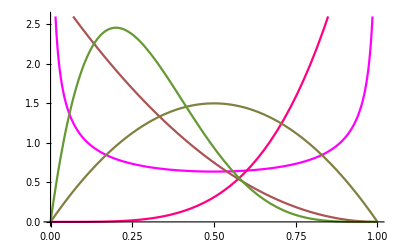

```mathematica
Print["1.Функция плотности распределения"]
plist={}
For[i=1,i <= 5, i++,
p=Plot[f[t,Part[ab, i, 1], Part[ab, i, 2]], {t, 0,1}, PlotRange->{0, 2.6}, PlotStyle->RGBColor[1/(i/2),1-(1/i*2), 1/i ]];
Print["a: ", Part[ab, i, 1],"; b: ", Part[ab, i, 2]," ",FontColor -> RGBColor[1/(i/2),1-(1/i*2), 1/i ] ];
AppendTo[plist, p]
]
Show[Sequence@@plist]
```

Pirnt[2.Функция распределения]

{}

a: 0.5; b: 0.5 FontColor→RGBColor[2, -1, 1]

a: 5; b: 1 FontColor→RGBColor[1, 0, Rational[1, 2]]

a: 1; b: 3 FontColor→RGBColor[Rational[2, 3], Rational[1, 3], Rational[1, 3]]

a: 2; b: 2 FontColor→RGBColor[Rational[1, 2], Rational[1, 2], Rational[1, 4]]

a: 2; b: 5 FontColor→RGBColor[Rational[2, 5], Rational[3, 5], Rational[1, 5]]

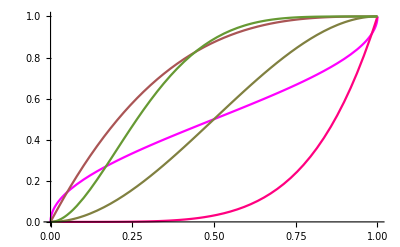

Графики обратной функции

{}

a: 0.5, b: 0.5

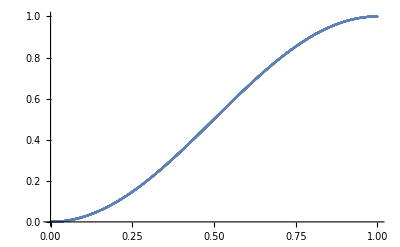

a: 5, b: 1

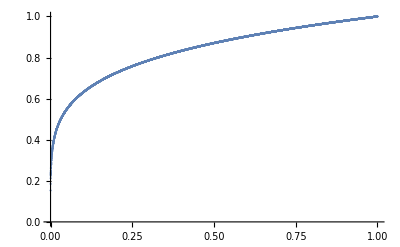

a: 1, b: 3

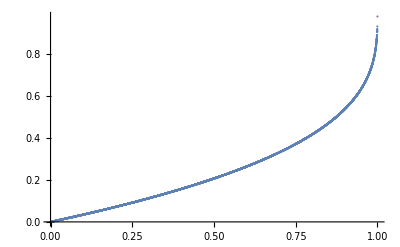

a: 2, b: 2

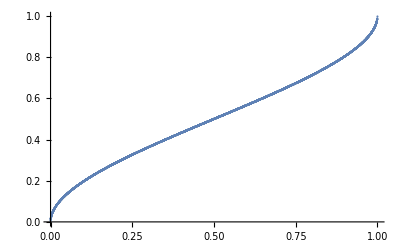

a: 2, b: 5

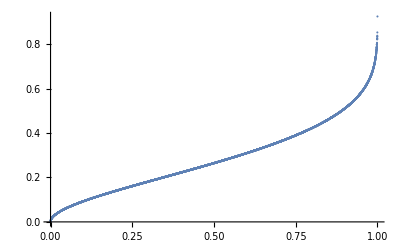

Гистограммы плотности распределения

a: 0.5, b: 0.5

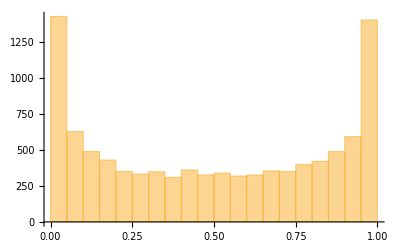

a: 5, b: 1

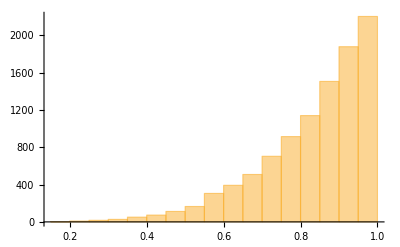

a: 1, b: 3

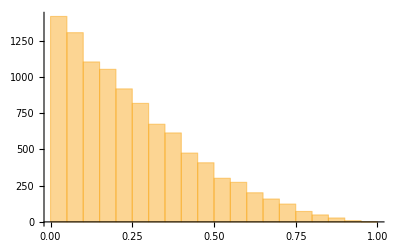

a: 2, b: 2

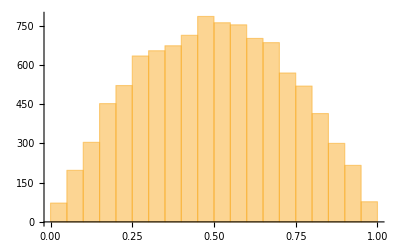

a: 2, b: 5

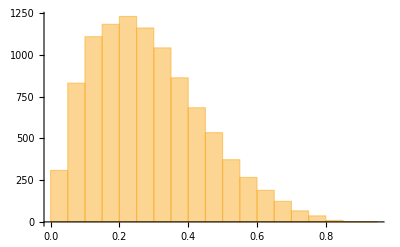

Сравнение мат ожиданий

0.498792

0.833458

0.249023

0.499361

0.28509

Mean1: 0.498792, theory mean: 0.5

Mean2: 0.833458, theory mean: 5/6

Mean3: 0.249023, theory mean: 1/4

Mean4: 0.499361, theory mean: 1/2

Mean5: 0.28509, theory mean: 2/7

Сравнение дисперсий

0.123957

0.0195533

0.037191

0.0494419

0.0252798

Variance1: 0.123957, theory variance: 0.125

Variance2: 0.0195533, theory variance: 5/252

Variance3: 0.037191, theory variance: 3/80

Variance4: 0.0494419, theory variance: 1/20

Variance5: 0.0252798, theory variance: 5/196

```mathematica
Pirnt["2.Функция распределения"]
plist={}
For[i=1,i <= 5, i++,
p=Plot[F[t,Part[ab, i, 1], Part[ab, i, 2]], {t, 0,1}, PlotRange->{0, 1}, PlotStyle->RGBColor[1/(i/2),1-(1/i*2), 1/i ]];
Print["a: ", Part[ab, i, 1],"; b: ", Part[ab, i, 2]," ",FontColor -> RGBColor[1/(i/2),1-(1/i*2), 1/i ] ];
AppendTo[plist, p]
]
Show[Sequence@@plist]


Print["Графики обратной функции"]
plist = {}

randFuncValArr1 = InverseBetaRegularized[randArr,Part[ab, 1,1],Part[ab, 1, 2]];
Print["a: ", Part[ab, 1,1],", b: ", Part[ab, 1, 2] ]
data = Transpose@{randArr, randFuncValArr1};
ListPlot[data]

randFuncValArr2 = InverseBetaRegularized[randArr,Part[ab, 2,1],Part[ab, 2, 2]];
Print["a: ", Part[ab, 2,1],", b: ", Part[ab, 2, 2] ]
data = Transpose@{randArr, randFuncValArr2};
ListPlot[data]

randFuncValArr3 = InverseBetaRegularized[randArr,Part[ab, 3,1],Part[ab, 3, 2]];
Print["a: ", Part[ab,3,1],", b: ", Part[ab, 3, 2] ]
data = Transpose@{randArr, randFuncValArr3};
ListPlot[data]

randFuncValArr4 = InverseBetaRegularized[randArr,Part[ab, 4,1],Part[ab, 4, 2]];
Print["a: ", Part[ab, 4,1],", b: ", Part[ab, 4, 2] ]
data = Transpose@{randArr, randFuncValArr4};
ListPlot[data]

randFuncValArr5 = InverseBetaRegularized[randArr,Part[ab, 5,1],Part[ab, 5, 2]];
Print["a: ", Part[ab, 5,1],", b: ", Part[ab, 5, 2] ]
data = Transpose@{randArr, randFuncValArr5};
ListPlot[data]





Print["Гистограммы плотности распределения"]

Print["a: ", Part[ab, 1,1],", b: ", Part[ab, 1, 2] ]
Histogram[{randFuncValArr1}, 20]
Print["a: ", Part[ab, 2,1],", b: ", Part[ab, 2, 2] ]
Histogram[{randFuncValArr2}, 20]
Print["a: ", Part[ab, 3,1],", b: ", Part[ab, 3, 2] ]
Histogram[{randFuncValArr3}, 20]
Print["a: ", Part[ab, 4,1],", b: ", Part[ab, 4, 2] ]
Histogram[{randFuncValArr4}, 20]
Print["a: ", Part[ab, 5,1],", b: ", Part[ab, 5, 2] ]
Histogram[{randFuncValArr5}, 20]

Print["Сравнение мат ожиданий"]
m1 = Total[randFuncValArr1] / arrSize
m2 = Total[randFuncValArr2] / arrSize
m3 = Total[randFuncValArr3] / arrSize
m4 = Total[randFuncValArr4] / arrSize
m5 = Total[randFuncValArr5] / arrSize
Print["Mean1: ", m1, ", theory mean: ", mean[Part[ab, 1,1], Part[ab, 1, 2] ]]
Print["Mean2: ", m2, ", theory mean: ", mean[Part[ab, 2,1], Part[ab, 2, 2] ]]
Print["Mean3: ", m3, ", theory mean: ", mean[Part[ab, 3,1], Part[ab, 3, 2] ]]
Print["Mean4: ", m4, ", theory mean: ", mean[Part[ab, 4,1], Part[ab, 4, 2] ]]
Print["Mean5: ", m5, ", theory mean: ", mean[Part[ab, 5,1], Part[ab, 5, 2] ]]

Print["Сравнение дисперсий"]
variance1 = (Total[randFuncValArr1^2] / arrSize) - (Total[randFuncValArr1] / arrSize) ^ 2
variance2 = (Total[randFuncValArr2^2] / arrSize) - (Total[randFuncValArr2] / arrSize) ^ 2
variance3 = (Total[randFuncValArr3^2] / arrSize) - (Total[randFuncValArr3] / arrSize) ^ 2
variance4 = (Total[randFuncValArr4^2] / arrSize) - (Total[randFuncValArr4] / arrSize) ^ 2
variance5= (Total[randFuncValArr5^2] / arrSize) - (Total[randFuncValArr5] / arrSize) ^ 2
Print["Variance1: ", variance1, ", theory variance: ", variance[Part[ab, 1,1], Part[ab, 1, 2] ]]
Print["Variance2: ", variance2, ", theory variance: ", variance[Part[ab, 2,1], Part[ab, 2, 2] ]]
Print["Variance3: ", variance3, ", theory variance: ", variance[Part[ab, 3,1], Part[ab, 3, 2] ]]
Print["Variance4: ", variance4, ", theory variance: ", variance[Part[ab, 4,1], Part[ab, 4, 2] ]]
Print["Variance5: ", variance5, ", theory variance: ", variance[Part[ab, 5,1], Part[ab, 5, 2] ]]
```